# Quantum states of systems of chemical interest using NDEigensystem

Single sentence description of the topic

## Hamiltonian operator for the Coulomb potential

Potential energy operator

```mathematica
𝒱(r__):=-1/Norm[{r}]
```

Kinetic energy operator:

```mathematica
𝒦(ψ_)(r__):=-1/2 ψ(r){r}
```

Hamiltonian operator:

```mathematica
ℋ(ψ_)(r__):=𝒦(ψ)(r)+𝒱(r) ψ(r)
```

#### Exercises:

Obtain the Hamiltonian for the Hydrogen atom in 1, 2, and 3 dimensions

Write the Schrodinger equation for the 1 dimensional Hydrogen atom.

## 1 Dimensional Hydrogen atom

### Analytical solutions

Schrodinger equation for the 1 dimensional Hydrogen atom can be written as Kummer’s equation. The solutions of Kummer’s equation are the confluent hypergeometric functions Hypergeometric1F1[1-n,2, 2 x/n] .

Analytical solutions:

```mathematica
Subscript[f, n_][x_]:=x Exp[-x/n]Hypergeometric1F1[1-n,2, 2 x/n]
```

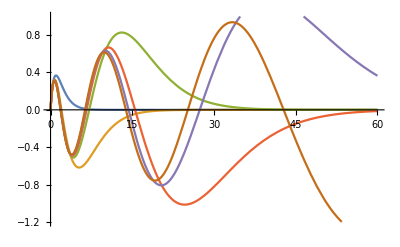

```mathematica
Plot[Evaluate@Table[Subscript[f, i][x],{i,1,6}],{x,0,60},PlotRange->{-1.2,1}]
```

In atomic units,the energies of the four lowest eigenstates are:

```mathematica
Subscript[ℰ, 1]=Table[N[-1/(2 i^2)],{i,1,6}]
```

{-0.5,-0.125,-0.0555556,-0.03125,-0.02,-0.0138889}

#### Exercises:

Are these functions normalized? If not, find the normalization constants for each eigenstate.

Define a normalized function.

#### Answer:

Find the normalization constant for each state:

```mathematica
nint=Table[NIntegrate[(Subscript[f, n][x])^2,{x,0,100}],{n,1,6}]
```

{0.25,2.,6.75,16.,31.25,53.9357}

The normalization constant is

```mathematica
norm=1/Sqrt[nint]
```

{2.,0.707107,0.3849,0.25,0.178886,0.136164}

Normalization:

```mathematica
Subscript[Ψ, n_][x_]:=norm⟦n⟧ Subscript[f, n][x]
```

```mathematica
Table[NIntegrate[  Subscript[Ψ, i][x]^2,{x,0,100}],{i,1,6}]
```

{1.,1.,1.,1.,1.,1.}

### Boundary conditions

Physically the probability of finding the electron at x=0 should be zero. Computationally, the wave function should be zero at the end of the computational box. These requirements can be fulfilled using Dirichlet Boundary conditions.

Boundary conditions:

```mathematica
Subscript[ℬ, 1]=DirichletCondition[ψ[x]==0,True];
```

In atomic units, the energies of the four lowest eigenstates are:

### Eigensystem

For a box of length l, the n lowest energy eigenstates are obtained with the function eigensystem[n,l]:

```mathematica
eigensystem1[ne_,ℓ_]:=
SortBy[
Transpose[
NDEigensystem[{ℋ[ψ][x],Subscript[ℬ, 1]},ψ,
{x,0,ℓ},ne,Method-> {"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}]],
First]
```

The eigenvalue (en) and the wave function can be obtained by using:

```mathematica
{en,wf}=eigensystem1[50,10]⟦1⟧
```

{-0.499998,InterpolatingFunction[{{0., 10.}}, <>]}

For example, for the ground state:

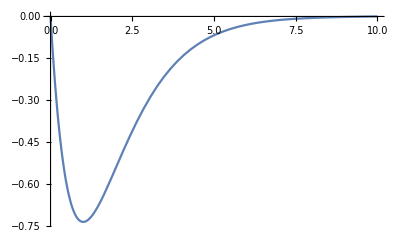

```mathematica
Plot[wf[x],{x,0,10}]
```

#### Exercise:

Verify that the eigenstates of eigensystem[n,l] are normalized.

Plot the ground state, and the first excited state. What are their energies?

#### Solution:

For example, for the 5th eigenstate obtained from a calculation of 10 states and a box of length 10 atomic units:

```mathematica
NIntegrate[(eigensystem1[10,10]⟦5,2⟧[x])^2,{x,0,10}]
```

1.

```mathematica
wf1=eigensystem1[10,10][[1,2]];
wf2=eigensystem1[10,10][[2,2]];
```

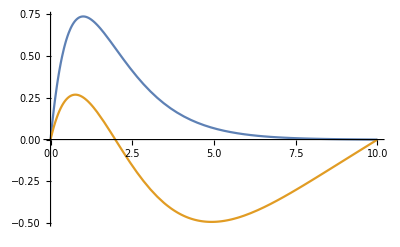

```mathematica
Plot[{wf1[x],wf2[x]},{x,0,10}]
```

### Results for the 4 lowest energy eigenstates

Quality of the eigenvalues and eigenvectors:

```mathematica
Manipulate[
GraphicsGrid@
Partition[
(es↦Table[
Show[
Plot[{es⟦i,1⟧+(es⟦i,2⟧[x])^2,𝒱[x],Subscript[ℰ, 1]⟦i⟧+(Subscript[Ψ, i][x]^2)},{x,0,40},
PlotRange->{-0.6,0.1},
Filling->{1->es⟦i,1⟧,2-> Bottom,None}]
],
{i,1,4}
])@
eigensystem1[ne,ℓ],
2],
{{ℓ,25,"Box Length"},5,40,5},
{{ne,15,"Number of eigenfunctions"},10,40,5}
]
```

#### Investigations

Use the sliding menus of the Manipulate to explore the solutions of NDEigensystem. Answer the following questions :

Determine the range in the parameters n and l for obtaining good agreement with the analytical results?

What should be the frequency of a photon to detach an electron in the 1D hydrogen atom?

What is the frequency of the emitted photon when the electron undergoes a transition between the first excited and the ground states?

## 2 Dimensional Hydrogen atom

### Analytical solutions

#### Radial function:

The analytical radial functions are given by R[n,l,r]

```mathematica
β[n_]=2/(n-1/2);
Ν[n_,l_]:=(((n+Abs[l]-1)!)/((2 n-1)(n-Abs[l]-1)!))^(1/2);
R[n_,l_,r_]:=β[n]/((2 l)!)Ν[n,l](β[n] r)^Abs[l] Exp[-β[n] r/2]Hypergeometric1F1[-n+Abs[l]+1,2 Abs[l]+1,β[n] r];
```

Radial wave functions for l=0:

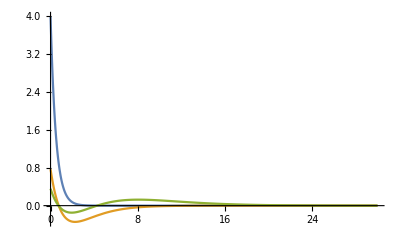

```mathematica
plotRa=Plot[Evaluate@Table[R[i,0,x],{i,1,3}],{x,0,30},PlotRange->All]
```

Radial wave functions for l=1:

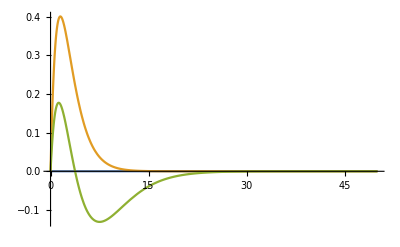

```mathematica
plotRa=Plot[Evaluate@Table[R[i,1,x],{i,1,3}],{x,0,50},PlotRange->All]
```

In atomic units, the energies of the four lowest ei
genstates are:

```mathematica
Subscript[ℰ, 2]=Table[-N[1/(2(n-1/2)^2)],{n,1,10}]
```

{-2.,-0.222222,-0.08,-0.0408163,-0.0246914,-0.0165289,-0.0118343,-0.00888889,-0.00692042,-0.00554017}

Degeneracy:

```mathematica
deg=Table[2(n-1)+1,{n,1,10}]
```

{1,3,5,7,9,11,13,15,17,19}

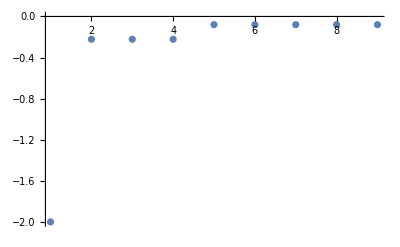

```mathematica
analyplot=ListPlot[Flatten[Table[Subscript[ℰ, 2]⟦i⟧,{i,1,3},{j,1,deg⟦i⟧}]],PlotRange->All]
```

#### Exercise

Are these functions normalized?

The wave function depends now on two quantum numbers. What is the meaning of them?

#### Answer

Numerical normalization

```mathematica
Column[Table[NIntegrate[r R[n,Abs[l],r]^2, {r,0,200}],{n,1,4},{l,-n+1,n-1}],Center ]
```

{1.}
{1.,1.,1.}
{1.,1.,1.,1.,1.}
{1.,1.,1.,1.,1.,1.,1.}

Analytically:

```mathematica
∫_0^∞ ∫_0^(2 π) r (R(2,1,r))^2 Φ(1,ϕ)Φ(-1,ϕ)ⅆϕⅆr
```

∫_0^(2 π) Φ[-1,ϕ] Φ[1,ϕ]ⅆϕ

#### The angular function:

As we saw before, the angular part has the eigenfunctions:

```mathematica
Φ[l_,ϕ_]:=1/(√(2π))Exp[I l ϕ]
```

Plotting the angular functions Φ[l,ϕ]:

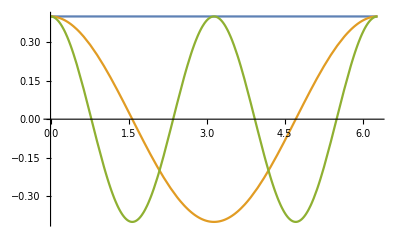

```mathematica
Plot[{Re[Φ[0,ϕ]],Re[Φ[1,ϕ]],Re[Φ[2,ϕ]]},{ϕ,0,2Pi}]
```

#### Exercise

Plot a graphics of the full wave function

Are these functions normalized?

Plot the ground state and first excited states, verify if the norm is one using polar and Cartesian coordinates.

#### Answer

The transformation from polar to Cartesian coordinates:

```mathematica
tocc=Thread[{r,ϕ}->ToPolarCoordinates[{x,y}]]
```

{r→√(x^2+y^2),ϕ→ArcTan[x,y]}

Plot the ground state:

```mathematica
Plot3D[Re[R[1,0,r]Φ[0,ϕ]]/.tocc,{x,-5,5},{y,-5,5},PlotRange->All]
```

-Graphics3D-

Verify for normalization:

```mathematica
NIntegrate[Abs[R[1,0,r]Φ[0,ϕ]]^2/.tocc,{x,-10,10},{y,-10,10}]
```

1.

Plot the first excited state with zero angular momentum:

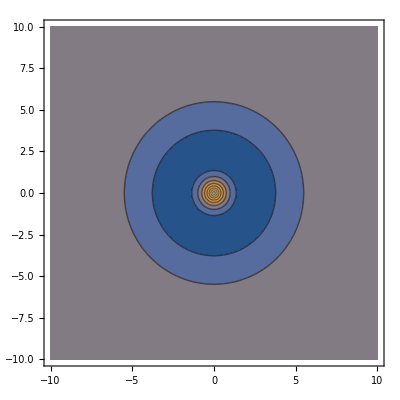

```mathematica
ContourPlot[Re[R[2,0,r]Φ[0,ϕ]]/.tocc,{x,-10,10},{y,-10,10},PlotRange->All,PlotPoints->25]
```

Verify the normalization in Cartesian coordinates:

```mathematica
NIntegrate[Abs[R[2,0,r]Φ[0,ϕ]]^2/.tocc,{x,-10,10},{y,-10,10}]
```

0.999351

Verify for normalization in polar coordinates

```mathematica
NIntegrate[r Abs[R[2,0,r]Φ[0,ϕ]]^2,{r,0,10},{ϕ,0,2 π}]
```

0.998601

Plot a state with l=1:

```mathematica
Plot3D[Im[R[2,1,r]Φ[1,ϕ]]/.tocc,{x,-10,10},{y,-10,10},PlotRange->All]
```

-Graphics3D-

Verify normalization in polar coordinates:

```mathematica
NIntegrate[r Abs[R[2,1,r]Φ[1,ϕ]]^2,{r,0,10},{ϕ,0,2 π}]
```

0.999193

Verify normalization in Cartesian coordinates:

```mathematica
NIntegrate[Abs[R[2,1,r]Φ[1,ϕ]]^2/.tocc,{x,-20,20},{y,-20,20}]
```

1.

### Boundary conditions and integration region

The analytical solutions showed that there are two types of states:
- even states which are not zero at the origin
- odd states which are zero at the origin

The Dirichlet Boundary condition for the even and odd states is given by:

```mathematica
Subscript[ℬ, 2]=DirichletCondition[ψ[x,y]==0,True]
```

DirichletCondition[ψ[x,y]==0,True]

With the integration region:

```mathematica
Subscript[𝒜, 2][Rin_,Rout_]:=Annulus[{0,0},{Rin,Rout}]
```

```mathematica
Subscript[𝒟, 2][R_]:=Disk[{0,0},R];
```

The integration region looks like:

-Graphics-



```mathematica
Graphics[Subscript[𝒜, 2][0.1,1]]
Graphics[Subscript[𝒟, 2][1]]
```

#### Exercise:

Why the integration region has this form? Give a physical interpretation.

### Eigensystem with annular integration region

Define a function for the eigensystem. The number of eigenfunctions is ne, inner and outer radii of the annulus are Rin and Rout respectively:

```mathematica
eigensystem2a[ne_,Rin_,Rout_]:=
SortBy[
Transpose[NDEigensystem[{ℋ[ψ][x,y],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Subscript[𝒜, 2][Rin,Rout],ne,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}]],First]
```

Manipulate the parameters of the numerical calculation to obtain the ground state:

```mathematica
Manipulate[
(es↦
Table[
Show[
Plot3D[
es⟦i,2⟧,Evaluate[{x,y}∈Subscript[𝒜, 2][Rin,Rout]],PlotRange->All,PlotLabel->es⟦i,1⟧
]
]
,{i,1,4}
])@
eigensystem2a[ne,Rin,Rout],
{{Rin,0.01,"Internal radius"},0.001,0.101,0.01},{{Rout,5,"External radius"},3,103,1},
{{ne,45,"Number of eigenfunctions"},10,100,5}
]
```

#### Exercise

Find the values of the internal and external radii, and the number of eigenstates for obtaining a good approximation to the ground state.

What happened with the excited states for these parameters? How good are the numerical eigenvalues compared with the analytical ones?

For the parameters found, plot the energy of the states. Discuss about the degeneracy.

Find values of the parameters to obtain excited states.

#### Answer

```mathematica
eigensys1=eigensystem2a[45,0.001,4];
```

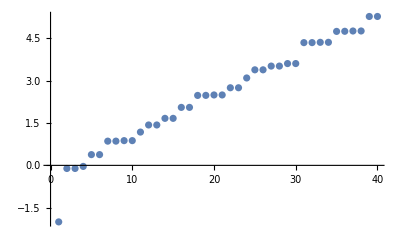

```mathematica
ListPlot[Table[{i,eigensys1⟦i,1⟧},{i,1,40}]]
```

### Eigensystem with disk integration region

Define a function for the eigensystem. The number of eigenfunctions is ne, and the radius of the disk R:

```mathematica
eigensystem2d[ne_,R_]:=
SortBy[
Transpose[NDEigensystem[{ℋ[ψ][x,y],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Subscript[𝒟, 2][R],ne,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}]],First]
```

Manipulate the parameters of the numerical calculation to obtain the ground state:

```mathematica
Manipulate[
(es↦
Table[
Show[
Plot3D[
es⟦i,2⟧,Evaluate[{x,y}∈Subscript[𝒟, 2][R]],PlotRange->All,PlotLabel->es⟦i,1⟧
]
]
,{i,1,4}
])@
eigensystem2d[ne,R],
{{R,5,"Radius of the Disk"},3,103,1},
{{ne,45,"Number of eigenfunctions"},10,100,5}
]
```

#### Exercise

Find the values of R, and the number of eigenstates for obtaining a good approximation to the ground state.

What happened with the excited states for these parameters? How good are the numerical eigenvalues compared with the analytical ones?

For the parameters found, plot the energy of the states. Discuss about the degeneracy.

Compare the results of using an annulus or a disk as integration region.

Find values of the parameters to obtain excited states.

#### Answer

```mathematica
eigensys2=eigensystem2d[45,5];
```

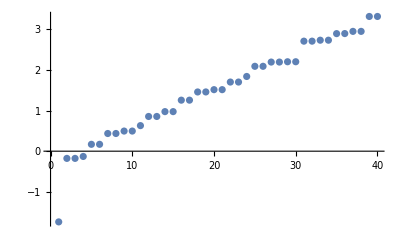

```mathematica
ListPlot[Table[{i,eigensys2⟦i,1⟧},{i,1,40}]]
```

### Diagram of the potential energy surface and the ground state

Calculate the states for a Disk of radius 5:

```mathematica
esys=Table[eigensystem2d[45,5][[i]],{i,1,6}];
```

The ground state:

```mathematica
fst1=Plot3D[esys[[1,1]]+0.3Abs[esys[[1,2]]],Evaluate[{x,y}∈Disk[{0,0},2,{-Pi,Pi}]],PlotRange->All,PlotPoints->45,PlotStyle->{White,Opacity[0.8]},MeshStyle->Black]
```

-Graphics3D-

Potential energy surface:

```mathematica
fpot=Plot3D[𝒱[x,y],{x,y}∈Disk[{0,0},10,{-Pi,Pi}],PlotRange->{-2.1,0.},PlotStyle->{Opacity[0.6],Black},PlotPoints->50,MeshStyle->Gray,ColorFunction->Function[{x,y,z},RGBColor[3z, 3z,3z]],Boxed->False]
```

-Graphics3D-

The ground state in the potential energy surface:

```mathematica
Show[fpot,fst1, PlotRange->All]
```

-Graphics3D-

## 1 Dimensional Hydrogen molecule ion: H_2^+

### Hamiltonian: regularization of the Coulomb potential

Potential energy operator

```mathematica
𝒱(r__,r1__,r2__,α_):=-1/(√(Norm[{r}-{r1}]+α^2))-1/(√(Norm[{r}-{r2}]+α^2))+1/Norm[{r2}-{r1}]
```

Kinetic energy operator:

```mathematica
𝒦[ψ_][r__]:=-1/2 ψ[r]{r}
```

Hamiltonian operator:

```mathematica
ℋ(ψ_)(r__,r1__,r2__,α_):=ψ(r) 𝒱(r,r1,r2,α)+𝒦(ψ)(r)
```

```mathematica
ℋ[ψ][x,r1,r2,a]
```

(1/Abs[-r1+r2]-1/(√(a^2+Abs[-r1+x]))-1/(√(a^2+Abs[-r2+x]))) ψ[x]-ψ''[x]/2

```mathematica
ℋ[ψ][{x,y},{r1x,r1y},{r2x,r2y},a]
```

-1/2 ψ[{x,y}]{{x,y}}+(1/(√((-r1x+r2x) (-Conjugate[r1x]+Conjugate[r2x])+(-r1y+r2y) (-Conjugate[r1y]+Conjugate[r2y])))-1/(√(a^2+√((-r1x+x) (-Conjugate[r1x]+Conjugate[x])+(-r1y+y) (-Conjugate[r1y]+Conjugate[y]))))-1/(√(a^2+√((-r2x+x) (-Conjugate[r2x]+Conjugate[x])+(-r2y+y) (-Conjugate[r2y]+Conjugate[y]))))) ψ[{x,y}]

A parameter α is necessary to regularize the potential energy to avoid the potential energy to blow up at singularities.

```mathematica
Manipulate[
Plot[{𝒱[x,-r/2,r/2,α],𝒱[x,-r/2,r/2,0]},{x,-5,5},PlotRange->{-6,0}],{{r,1,"Bond Length"},1,4,0.1},{{α,0.1,"Regularization Parameter"},0,1,0.1}
]
```

#### Exercises:

Find a good value for α

Plot the potential energy of H_2^+  in 1 and 2 dimensions

Obtain the Hamiltonian for the H_2^+ in 1, 2, and 3 dimensions.

Write the Schrodinger equation for the 1 dimensional H_2^+.

#### Answer:

Potential energy:

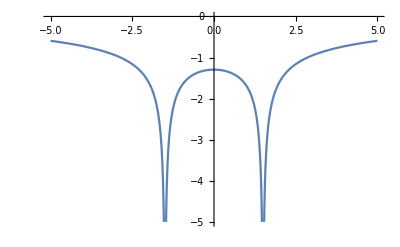

```mathematica
Plot[𝒱[x,-1.5,1.5,0.1],{x,-5,5},PlotRange->{-5,0}]
```

The potential energy in 2 dimensions:

```mathematica
Plot3D[𝒱[{x,y},{-1.5,0},{1.5,0},0.1],{x,-4,4},{y,-4,4},PlotRange->{-3,0}]
```

-Graphics3D-

### Eigensystem

The function eigensystem[l,𝓇,ne], finds ne eigenvalues of the H_2^+ for a internuclear distance 𝓇 in a computational box of length 2ℓ+𝓇 :

```mathematica
eigensystem3[ℓ_,𝓇_,ne_]:=
SortBy[
Transpose[
NDEigensystem[{ℋ[ψ][x,-𝓇/2,𝓇/2,0.1],DirichletCondition[ψ[x]==0,True]},ψ,
{x,-ℓ,ℓ},ne,Method-> {"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}}}]],
First]
```

The ground electronic state:

```mathematica
{en,wf}=eigensystem3[8.001,4,60][[1]]
```

{-1.98096,InterpolatingFunction[{{-8.001, 8.001}}, <>]}

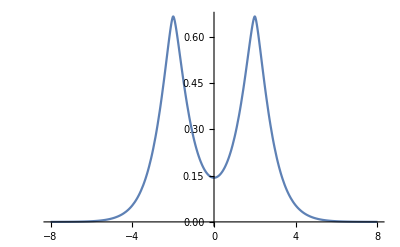

```mathematica
Plot[wf[x],{x,-10,10},PlotRange->All]
```

The first excited electronic state:

```mathematica
{en,wf}=eigensystem3[8,4,60][[2]]
```

{-1.95334,InterpolatingFunction[{{-8., 8.}}, <>]}

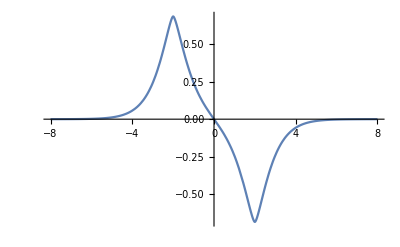

```mathematica
Plot[wf[x],{x,-10,10},PlotRange->All]
```

```mathematica
Manipulate[
GraphicsGrid@
Partition[
(es↦Table[
Show[
Plot[{es⟦i,1⟧+(es⟦i,2⟧[x]),𝒱[x,-𝓇/2,𝓇/2,0.1]},{x,-ℓ,ℓ},
Filling->{1->es⟦i,1⟧,2-> Bottom},PlotPoints->20,PlotRange->{le,le+ΔE}]
],
{i,1,4}
])@
eigensystem3[ℓ,𝓇,ne],
2],
{{ℓ,10,"Box Length"},10,20,1},
{{𝓇,2,"Bond Length"},1.,6.,0.5},
{{ne,40,"Number of eigenfunctions"},40,100,5},
{{le,-2,"Lowest Energy"},-10,0,0.5},
{{ΔE,3,"Energy range"},1,20,2}
]
```

### Born Oppenheimer curves

The energy of the electronic states as a function of the internuclear distance gives the Born-Oppenheimer curves:

```mathematica
Clear[databo];databo[a_]:=databo[a]=eigensystem3[a/2+10,a,50];
```

```mathematica
tablebo=Table[Flatten[{a,Table[databo[a]⟦i,1⟧,{i,1,4}]}],{a,0.5,25.,0.2}];
```

Ground state:

```mathematica
tground=Table[
{tablebo⟦i,1⟧,tablebo⟦i,2⟧},
{i,1,Length[tablebo]}
];
```

Plot the ground state:

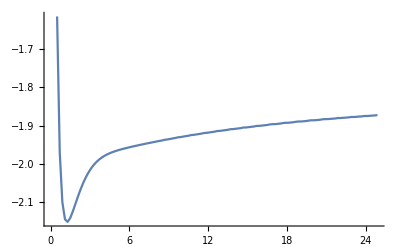

```mathematica
ground=ListLinePlot[tground,PlotRange->All]
```

First excited state

```mathematica
tfirst=Table[{tablebo⟦i,1⟧,tablebo⟦i,3⟧},{i,1,Length[tablebo]}];
```

Plot the first excited state:

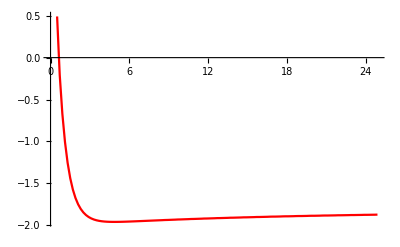

```mathematica
firste=ListLinePlot[tfirst,PlotStyle->Red,PlotRange->All]
```

The lowest electronic states (sigma)

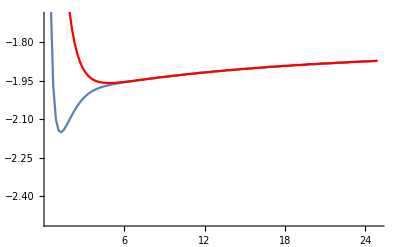

```mathematica
Show[ground,firste,PlotRange->{-2.5,-1.7}]
```

#### Exercise:

Calculate the ionization energy for the hydrogen molecular ion.

Calculate the bond dissociation energy

Compare your result with the experimental value (bond length 2 atomic units and dissociation energy 2.79 eV)

Analyze the asymptotic wave functions for the ground and first excite levels

#### Answer:

Find the lowest energy:

```mathematica
ming=Min[tground]
```

Min[0.5,-1/2 ψ[x]{x,0.5,z}+(2.-1/(√(0.01+Abs[-0.25+x]))-1/(√(0.01+Abs[0.25+x]))) ψ[x],-1/2 ψ[x]{x,0.7,z}+(1.42857-1/(√(0.01+Abs[-0.35+x]))-1/(√(0.01+Abs[0.35+x]))) ψ[x],-1/2 ψ[x]{x,0.9,z}+(1.11111-1/(√(0.01+Abs[-0.45+x]))-1/(√(0.01+Abs[0.45+x]))) ψ[x],-1/2 ψ[x]{x,1.1,z}+(0.909091-1/(√(0.01+Abs[-0.55+x]))-1/(√(0.01+Abs[0.55+x]))) ψ[x],-1/2 ψ[x]{x,1.3,z}+(0.769231-1/(√(0.01+Abs[-0.65+x]))-1/(√(0.01+Abs[0.65+x]))) ψ[x],-1/2 ψ[x]{x,1.5,z}+(0.666667-1/(√(0.01+Abs[-0.75+x]))-1/(√(0.01+Abs[0.75+x]))) ψ[x],-1/2 ψ[x]{x,1.7,z}+(0.588235-1/(√(0.01+Abs[-0.85+x]))-1/(√(0.01+Abs[0.85+x]))) ψ[x],-1/2 ψ[x]{x,1.9,z}+(0.526316-1/(√(0.01+Abs[-0.95+x]))-1/(√(0.01+Abs[0.95+x]))) ψ[x],-1/2 ψ[x]{x,2.1,z}+(0.47619-1/(√(0.01+Abs[-1.05+x]))-1/(√(0.01+Abs[1.05+x]))) ψ[x],-1/2 ψ[x]{x,2.3,z}+(0.434783-1/(√(0.01+Abs[-1.15+x]))-1/(√(0.01+Abs[1.15+x]))) ψ[x],-1/2 ψ[x]{x,2.5,z}+(0.4-1/(√(0.01+Abs[-1.25+x]))-1/(√(0.01+Abs[1.25+x]))) ψ[x],-1/2 ψ[x]{x,2.7,z}+(0.37037-1/(√(0.01+Abs[-1.35+x]))-1/(√(0.01+Abs[1.35+x]))) ψ[x],-1/2 ψ[x]{x,2.9,z}+(0.344828-1/(√(0.01+Abs[-1.45+x]))-1/(√(0.01+Abs[1.45+x]))) ψ[x],-1/2 ψ[x]{x,3.1,z}+(0.322581-1/(√(0.01+Abs[-1.55+x]))-1/(√(0.01+Abs[1.55+x]))) ψ[x],-1/2 ψ[x]{x,3.3,z}+(0.30303-1/(√(0.01+Abs[-1.65+x]))-1/(√(0.01+Abs[1.65+x]))) ψ[x],-1/2 ψ[x]{x,3.5,z}+(0.285714-1/(√(0.01+Abs[-1.75+x]))-1/(√(0.01+Abs[1.75+x]))) ψ[x],-1/2 ψ[x]{x,3.7,z}+(0.27027-1/(√(0.01+Abs[-1.85+x]))-1/(√(0.01+Abs[1.85+x]))) ψ[x],-1/2 ψ[x]{x,3.9,z}+(0.25641-1/(√(0.01+Abs[-1.95+x]))-1/(√(0.01+Abs[1.95+x]))) ψ[x],-1/2 ψ[x]{x,4.1,z}+(0.243902-1/(√(0.01+Abs[-2.05+x]))-1/(√(0.01+Abs[2.05+x]))) ψ[x],-1/2 ψ[x]{x,4.3,z}+(0.232558-1/(√(0.01+Abs[-2.15+x]))-1/(√(0.01+Abs[2.15+x]))) ψ[x],-1/2 ψ[x]{x,4.5,z}+(0.222222-1/(√(0.01+Abs[-2.25+x]))-1/(√(0.01+Abs[2.25+x]))) ψ[x],-1/2 ψ[x]{x,4.7,z}+(0.212766-1/(√(0.01+Abs[-2.35+x]))-1/(√(0.01+Abs[2.35+x]))) ψ[x],-1/2 ψ[x]{x,4.9,z}+(0.204082-1/(√(0.01+Abs[-2.45+x]))-1/(√(0.01+Abs[2.45+x]))) ψ[x],-1/2 ψ[x]{x,5.1,z}+(0.196078-1/(√(0.01+Abs[-2.55+x]))-1/(√(0.01+Abs[2.55+x]))) ψ[x],-1/2 ψ[x]{x,5.3,z}+(0.188679-1/(√(0.01+Abs[-2.65+x]))-1/(√(0.01+Abs[2.65+x]))) ψ[x],-1/2 ψ[x]{x,5.5,z}+(0.181818-1/(√(0.01+Abs[-2.75+x]))-1/(√(0.01+Abs[2.75+x]))) ψ[x],-1/2 ψ[x]{x,5.7,z}+(0.175439-1/(√(0.01+Abs[-2.85+x]))-1/(√(0.01+Abs[2.85+x]))) ψ[x],-1/2 ψ[x]{x,5.9,z}+(0.169492-1/(√(0.01+Abs[-2.95+x]))-1/(√(0.01+Abs[2.95+x]))) ψ[x],-1/2 ψ[x]{x,6.1,z}+(0.163934-1/(√(0.01+Abs[-3.05+x]))-1/(√(0.01+Abs[3.05+x]))) ψ[x],-1/2 ψ[x]{x,6.3,z}+(0.15873-1/(√(0.01+Abs[-3.15+x]))-1/(√(0.01+Abs[3.15+x]))) ψ[x],-1/2 ψ[x]{x,6.5,z}+(0.153846-1/(√(0.01+Abs[-3.25+x]))-1/(√(0.01+Abs[3.25+x]))) ψ[x],-1/2 ψ[x]{x,6.7,z}+(0.149254-1/(√(0.01+Abs[-3.35+x]))-1/(√(0.01+Abs[3.35+x]))) ψ[x],-1/2 ψ[x]{x,6.9,z}+(0.144928-1/(√(0.01+Abs[-3.45+x]))-1/(√(0.01+Abs[3.45+x]))) ψ[x],-1/2 ψ[x]{x,7.1,z}+(0.140845-1/(√(0.01+Abs[-3.55+x]))-1/(√(0.01+Abs[3.55+x]))) ψ[x],-1/2 ψ[x]{x,7.3,z}+(0.136986-1/(√(0.01+Abs[-3.65+x]))-1/(√(0.01+Abs[3.65+x]))) ψ[x],-1/2 ψ[x]{x,7.5,z}+(0.133333-1/(√(0.01+Abs[-3.75+x]))-1/(√(0.01+Abs[3.75+x]))) ψ[x],-1/2 ψ[x]{x,7.7,z}+(0.12987-1/(√(0.01+Abs[-3.85+x]))-1/(√(0.01+Abs[3.85+x]))) ψ[x],-1/2 ψ[x]{x,7.9,z}+(0.126582-1/(√(0.01+Abs[-3.95+x]))-1/(√(0.01+Abs[3.95+x]))) ψ[x],-1/2 ψ[x]{x,8.1,z}+(0.123457-1/(√(0.01+Abs[-4.05+x]))-1/(√(0.01+Abs[4.05+x]))) ψ[x],-1/2 ψ[x]{x,8.3,z}+(0.120482-1/(√(0.01+Abs[-4.15+x]))-1/(√(0.01+Abs[4.15+x]))) ψ[x],-1/2 ψ[x]{x,8.5,z}+(0.117647-1/(√(0.01+Abs[-4.25+x]))-1/(√(0.01+Abs[4.25+x]))) ψ[x],-1/2 ψ[x]{x,8.7,z}+(0.114943-1/(√(0.01+Abs[-4.35+x]))-1/(√(0.01+Abs[4.35+x]))) ψ[x],-1/2 ψ[x]{x,8.9,z}+(0.11236-1/(√(0.01+Abs[-4.45+x]))-1/(√(0.01+Abs[4.45+x]))) ψ[x],-1/2 ψ[x]{x,9.1,z}+(0.10989-1/(√(0.01+Abs[-4.55+x]))-1/(√(0.01+Abs[4.55+x]))) ψ[x],-1/2 ψ[x]{x,9.3,z}+(0.107527-1/(√(0.01+Abs[-4.65+x]))-1/(√(0.01+Abs[4.65+x]))) ψ[x],-1/2 ψ[x]{x,9.5,z}+(0.105263-1/(√(0.01+Abs[-4.75+x]))-1/(√(0.01+Abs[4.75+x]))) ψ[x],-1/2 ψ[x]{x,9.7,z}+(0.103093-1/(√(0.01+Abs[-4.85+x]))-1/(√(0.01+Abs[4.85+x]))) ψ[x],-1/2 ψ[x]{x,9.9,z}+(0.10101-1/(√(0.01+Abs[-4.95+x]))-1/(√(0.01+Abs[4.95+x]))) ψ[x],-1/2 ψ[x]{x,10.1,z}+(0.0990099-1/(√(0.01+Abs[-5.05+x]))-1/(√(0.01+Abs[5.05+x]))) ψ[x],-1/2 ψ[x]{x,10.3,z}+(0.0970874-1/(√(0.01+Abs[-5.15+x]))-1/(√(0.01+Abs[5.15+x]))) ψ[x],-1/2 ψ[x]{x,10.5,z}+(0.0952381-1/(√(0.01+Abs[-5.25+x]))-1/(√(0.01+Abs[5.25+x]))) ψ[x],-1/2 ψ[x]{x,10.7,z}+(0.0934579-1/(√(0.01+Abs[-5.35+x]))-1/(√(0.01+Abs[5.35+x]))) ψ[x],-1/2 ψ[x]{x,10.9,z}+(0.0917431-1/(√(0.01+Abs[-5.45+x]))-1/(√(0.01+Abs[5.45+x]))) ψ[x],-1/2 ψ[x]{x,11.1,z}+(0.0900901-1/(√(0.01+Abs[-5.55+x]))-1/(√(0.01+Abs[5.55+x]))) ψ[x],-1/2 ψ[x]{x,11.3,z}+(0.0884956-1/(√(0.01+Abs[-5.65+x]))-1/(√(0.01+Abs[5.65+x]))) ψ[x],-1/2 ψ[x]{x,11.5,z}+(0.0869565-1/(√(0.01+Abs[-5.75+x]))-1/(√(0.01+Abs[5.75+x]))) ψ[x],-1/2 ψ[x]{x,11.7,z}+(0.0854701-1/(√(0.01+Abs[-5.85+x]))-1/(√(0.01+Abs[5.85+x]))) ψ[x],-1/2 ψ[x]{x,11.9,z}+(0.0840336-1/(√(0.01+Abs[-5.95+x]))-1/(√(0.01+Abs[5.95+x]))) ψ[x],-1/2 ψ[x]{x,12.1,z}+(0.0826446-1/(√(0.01+Abs[-6.05+x]))-1/(√(0.01+Abs[6.05+x]))) ψ[x],-1/2 ψ[x]{x,12.3,z}+(0.0813008-1/(√(0.01+Abs[-6.15+x]))-1/(√(0.01+Abs[6.15+x]))) ψ[x],-1/2 ψ[x]{x,12.5,z}+(0.08-1/(√(0.01+Abs[-6.25+x]))-1/(√(0.01+Abs[6.25+x]))) ψ[x],-1/2 ψ[x]{x,12.7,z}+(0.0787402-1/(√(0.01+Abs[-6.35+x]))-1/(√(0.01+Abs[6.35+x]))) ψ[x],-1/2 ψ[x]{x,12.9,z}+(0.0775194-1/(√(0.01+Abs[-6.45+x]))-1/(√(0.01+Abs[6.45+x]))) ψ[x],-1/2 ψ[x]{x,13.1,z}+(0.0763359-1/(√(0.01+Abs[-6.55+x]))-1/(√(0.01+Abs[6.55+x]))) ψ[x],-1/2 ψ[x]{x,13.3,z}+(0.075188-1/(√(0.01+Abs[-6.65+x]))-1/(√(0.01+Abs[6.65+x]))) ψ[x],-1/2 ψ[x]{x,13.5,z}+(0.0740741-1/(√(0.01+Abs[-6.75+x]))-1/(√(0.01+Abs[6.75+x]))) ψ[x],-1/2 ψ[x]{x,13.7,z}+(0.0729927-1/(√(0.01+Abs[-6.85+x]))-1/(√(0.01+Abs[6.85+x]))) ψ[x],-1/2 ψ[x]{x,13.9,z}+(0.0719424-1/(√(0.01+Abs[-6.95+x]))-1/(√(0.01+Abs[6.95+x]))) ψ[x],-1/2 ψ[x]{x,14.1,z}+(0.070922-1/(√(0.01+Abs[-7.05+x]))-1/(√(0.01+Abs[7.05+x]))) ψ[x],-1/2 ψ[x]{x,14.3,z}+(0.0699301-1/(√(0.01+Abs[-7.15+x]))-1/(√(0.01+Abs[7.15+x]))) ψ[x],-1/2 ψ[x]{x,14.5,z}+(0.0689655-1/(√(0.01+Abs[-7.25+x]))-1/(√(0.01+Abs[7.25+x]))) ψ[x],-1/2 ψ[x]{x,14.7,z}+(0.0680272-1/(√(0.01+Abs[-7.35+x]))-1/(√(0.01+Abs[7.35+x]))) ψ[x],-1/2 ψ[x]{x,14.9,z}+(0.0671141-1/(√(0.01+Abs[-7.45+x]))-1/(√(0.01+Abs[7.45+x]))) ψ[x],-1/2 ψ[x]{x,15.1,z}+(0.0662252-1/(√(0.01+Abs[-7.55+x]))-1/(√(0.01+Abs[7.55+x]))) ψ[x],-1/2 ψ[x]{x,15.3,z}+(0.0653595-1/(√(0.01+Abs[-7.65+x]))-1/(√(0.01+Abs[7.65+x]))) ψ[x],-1/2 ψ[x]{x,15.5,z}+(0.0645161-1/(√(0.01+Abs[-7.75+x]))-1/(√(0.01+Abs[7.75+x]))) ψ[x],-1/2 ψ[x]{x,15.7,z}+(0.0636943-1/(√(0.01+Abs[-7.85+x]))-1/(√(0.01+Abs[7.85+x]))) ψ[x],-1/2 ψ[x]{x,15.9,z}+(0.0628931-1/(√(0.01+Abs[-7.95+x]))-1/(√(0.01+Abs[7.95+x]))) ψ[x],-1/2 ψ[x]{x,16.1,z}+(0.0621118-1/(√(0.01+Abs[-8.05+x]))-1/(√(0.01+Abs[8.05+x]))) ψ[x],-1/2 ψ[x]{x,16.3,z}+(0.0613497-1/(√(0.01+Abs[-8.15+x]))-1/(√(0.01+Abs[8.15+x]))) ψ[x],-1/2 ψ[x]{x,16.5,z}+(0.0606061-1/(√(0.01+Abs[-8.25+x]))-1/(√(0.01+Abs[8.25+x]))) ψ[x],-1/2 ψ[x]{x,16.7,z}+(0.0598802-1/(√(0.01+Abs[-8.35+x]))-1/(√(0.01+Abs[8.35+x]))) ψ[x],-1/2 ψ[x]{x,16.9,z}+(0.0591716-1/(√(0.01+Abs[-8.45+x]))-1/(√(0.01+Abs[8.45+x]))) ψ[x],-1/2 ψ[x]{x,17.1,z}+(0.0584795-1/(√(0.01+Abs[-8.55+x]))-1/(√(0.01+Abs[8.55+x]))) ψ[x],-1/2 ψ[x]{x,17.3,z}+(0.0578035-1/(√(0.01+Abs[-8.65+x]))-1/(√(0.01+Abs[8.65+x]))) ψ[x],-1/2 ψ[x]{x,17.5,z}+(0.0571429-1/(√(0.01+Abs[-8.75+x]))-1/(√(0.01+Abs[8.75+x]))) ψ[x],-1/2 ψ[x]{x,17.7,z}+(0.0564972-1/(√(0.01+Abs[-8.85+x]))-1/(√(0.01+Abs[8.85+x]))) ψ[x],-1/2 ψ[x]{x,17.9,z}+(0.0558659-1/(√(0.01+Abs[-8.95+x]))-1/(√(0.01+Abs[8.95+x]))) ψ[x],-1/2 ψ[x]{x,18.1,z}+(0.0552486-1/(√(0.01+Abs[-9.05+x]))-1/(√(0.01+Abs[9.05+x]))) ψ[x],-1/2 ψ[x]{x,18.3,z}+(0.0546448-1/(√(0.01+Abs[-9.15+x]))-1/(√(0.01+Abs[9.15+x]))) ψ[x],-1/2 ψ[x]{x,18.5,z}+(0.0540541-1/(√(0.01+Abs[-9.25+x]))-1/(√(0.01+Abs[9.25+x]))) ψ[x],-1/2 ψ[x]{x,18.7,z}+(0.0534759-1/(√(0.01+Abs[-9.35+x]))-1/(√(0.01+Abs[9.35+x]))) ψ[x],-1/2 ψ[x]{x,18.9,z}+(0.0529101-1/(√(0.01+Abs[-9.45+x]))-1/(√(0.01+Abs[9.45+x]))) ψ[x],-1/2 ψ[x]{x,19.1,z}+(0.052356-1/(√(0.01+Abs[-9.55+x]))-1/(√(0.01+Abs[9.55+x]))) ψ[x],-1/2 ψ[x]{x,19.3,z}+(0.0518135-1/(√(0.01+Abs[-9.65+x]))-1/(√(0.01+Abs[9.65+x]))) ψ[x],-1/2 ψ[x]{x,19.5,z}+(0.0512821-1/(√(0.01+Abs[-9.75+x]))-1/(√(0.01+Abs[9.75+x]))) ψ[x],-1/2 ψ[x]{x,19.7,z}+(0.0507614-1/(√(0.01+Abs[-9.85+x]))-1/(√(0.01+Abs[9.85+x]))) ψ[x],-1/2 ψ[x]{x,19.9,z}+(0.0502513-1/(√(0.01+Abs[-9.95+x]))-1/(√(0.01+Abs[9.95+x]))) ψ[x],-1/2 ψ[x]{x,20.1,z}+(0.0497512-1/(√(0.01+Abs[-10.05+x]))-1/(√(0.01+Abs[10.05+x]))) ψ[x],-1/2 ψ[x]{x,20.3,z}+(0.0492611-1/(√(0.01+Abs[-10.15+x]))-1/(√(0.01+Abs[10.15+x]))) ψ[x],-1/2 ψ[x]{x,20.5,z}+(0.0487805-1/(√(0.01+Abs[-10.25+x]))-1/(√(0.01+Abs[10.25+x]))) ψ[x],-1/2 ψ[x]{x,20.7,z}+(0.0483092-1/(√(0.01+Abs[-10.35+x]))-1/(√(0.01+Abs[10.35+x]))) ψ[x],-1/2 ψ[x]{x,20.9,z}+(0.0478469-1/(√(0.01+Abs[-10.45+x]))-1/(√(0.01+Abs[10.45+x]))) ψ[x],-1/2 ψ[x]{x,21.1,z}+(0.0473934-1/(√(0.01+Abs[-10.55+x]))-1/(√(0.01+Abs[10.55+x]))) ψ[x],-1/2 ψ[x]{x,21.3,z}+(0.0469484-1/(√(0.01+Abs[-10.65+x]))-1/(√(0.01+Abs[10.65+x]))) ψ[x],-1/2 ψ[x]{x,21.5,z}+(0.0465116-1/(√(0.01+Abs[-10.75+x]))-1/(√(0.01+Abs[10.75+x]))) ψ[x],-1/2 ψ[x]{x,21.7,z}+(0.0460829-1/(√(0.01+Abs[-10.85+x]))-1/(√(0.01+Abs[10.85+x]))) ψ[x],-1/2 ψ[x]{x,21.9,z}+(0.0456621-1/(√(0.01+Abs[-10.95+x]))-1/(√(0.01+Abs[10.95+x]))) ψ[x],-1/2 ψ[x]{x,22.1,z}+(0.0452489-1/(√(0.01+Abs[-11.05+x]))-1/(√(0.01+Abs[11.05+x]))) ψ[x],-1/2 ψ[x]{x,22.3,z}+(0.044843-1/(√(0.01+Abs[-11.15+x]))-1/(√(0.01+Abs[11.15+x]))) ψ[x],-1/2 ψ[x]{x,22.5,z}+(0.0444444-1/(√(0.01+Abs[-11.25+x]))-1/(√(0.01+Abs[11.25+x]))) ψ[x],-1/2 ψ[x]{x,22.7,z}+(0.0440529-1/(√(0.01+Abs[-11.35+x]))-1/(√(0.01+Abs[11.35+x]))) ψ[x],-1/2 ψ[x]{x,22.9,z}+(0.0436681-1/(√(0.01+Abs[-11.45+x]))-1/(√(0.01+Abs[11.45+x]))) ψ[x],-1/2 ψ[x]{x,23.1,z}+(0.04329-1/(√(0.01+Abs[-11.55+x]))-1/(√(0.01+Abs[11.55+x]))) ψ[x],-1/2 ψ[x]{x,23.3,z}+(0.0429185-1/(√(0.01+Abs[-11.65+x]))-1/(√(0.01+Abs[11.65+x]))) ψ[x],-1/2 ψ[x]{x,23.5,z}+(0.0425532-1/(√(0.01+Abs[-11.75+x]))-1/(√(0.01+Abs[11.75+x]))) ψ[x],-1/2 ψ[x]{x,23.7,z}+(0.0421941-1/(√(0.01+Abs[-11.85+x]))-1/(√(0.01+Abs[11.85+x]))) ψ[x],-1/2 ψ[x]{x,23.9,z}+(0.041841-1/(√(0.01+Abs[-11.95+x]))-1/(√(0.01+Abs[11.95+x]))) ψ[x],-1/2 ψ[x]{x,24.1,z}+(0.0414938-1/(√(0.01+Abs[-12.05+x]))-1/(√(0.01+Abs[12.05+x]))) ψ[x],-1/2 ψ[x]{x,24.3,z}+(0.0411523-1/(√(0.01+Abs[-12.15+x]))-1/(√(0.01+Abs[12.15+x]))) ψ[x],-1/2 ψ[x]{x,24.5,z}+(0.0408163-1/(√(0.01+Abs[-12.25+x]))-1/(√(0.01+Abs[12.25+x]))) ψ[x],-1/2 ψ[x]{x,24.7,z}+(0.0404858-1/(√(0.01+Abs[-12.35+x]))-1/(√(0.01+Abs[12.35+x]))) ψ[x],-1/2 ψ[x]{x,24.9,z}+(0.0401606-1/(√(0.01+Abs[-12.45+x]))-1/(√(0.01+Abs[12.45+x]))) ψ[x]]

```mathematica
minpos=Position[tground,ming]
```

{}

The energy necessary to photo-dissociate the molecule is:

```mathematica
photo=tfirst[[minpos[[1,1]]]]-tground[[minpos[[1,1]]]]
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

{{0.5,DirichletCondition[ψ[x]==0,True]},{0.7,DirichletCondition[ψ[x]==0,True]},{0.9,DirichletCondition[ψ[x]==0,True]},{1.1,DirichletCondition[ψ[x]==0,True]},{1.3,DirichletCondition[ψ[x]==0,True]},{1.5,DirichletCondition[ψ[x]==0,True]},{1.7,DirichletCondition[ψ[x]==0,True]},{1.9,DirichletCondition[ψ[x]==0,True]},{2.1,DirichletCondition[ψ[x]==0,True]},{2.3,DirichletCondition[ψ[x]==0,True]},{2.5,DirichletCondition[ψ[x]==0,True]},{2.7,DirichletCondition[ψ[x]==0,True]},{2.9,DirichletCondition[ψ[x]==0,True]},{3.1,DirichletCondition[ψ[x]==0,True]},{3.3,DirichletCondition[ψ[x]==0,True]},{3.5,DirichletCondition[ψ[x]==0,True]},{3.7,DirichletCondition[ψ[x]==0,True]},{3.9,DirichletCondition[ψ[x]==0,True]},{4.1,DirichletCondition[ψ[x]==0,True]},{4.3,DirichletCondition[ψ[x]==0,True]},{4.5,DirichletCondition[ψ[x]==0,True]},{4.7,DirichletCondition[ψ[x]==0,True]},{4.9,DirichletCondition[ψ[x]==0,True]},{5.1,DirichletCondition[ψ[x]==0,True]},{5.3,DirichletCondition[ψ[x]==0,True]},{5.5,DirichletCondition[ψ[x]==0,True]},{5.7,DirichletCondition[ψ[x]==0,True]},{5.9,DirichletCondition[ψ[x]==0,True]},{6.1,DirichletCondition[ψ[x]==0,True]},{6.3,DirichletCondition[ψ[x]==0,True]},{6.5,DirichletCondition[ψ[x]==0,True]},{6.7,DirichletCondition[ψ[x]==0,True]},{6.9,DirichletCondition[ψ[x]==0,True]},{7.1,DirichletCondition[ψ[x]==0,True]},{7.3,DirichletCondition[ψ[x]==0,True]},{7.5,DirichletCondition[ψ[x]==0,True]},{7.7,DirichletCondition[ψ[x]==0,True]},{7.9,DirichletCondition[ψ[x]==0,True]},{8.1,DirichletCondition[ψ[x]==0,True]},{8.3,DirichletCondition[ψ[x]==0,True]},{8.5,DirichletCondition[ψ[x]==0,True]},{8.7,DirichletCondition[ψ[x]==0,True]},{8.9,DirichletCondition[ψ[x]==0,True]},{9.1,DirichletCondition[ψ[x]==0,True]},{9.3,DirichletCondition[ψ[x]==0,True]},{9.5,DirichletCondition[ψ[x]==0,True]},{9.7,DirichletCondition[ψ[x]==0,True]},{9.9,DirichletCondition[ψ[x]==0,True]},{10.1,DirichletCondition[ψ[x]==0,True]},{10.3,DirichletCondition[ψ[x]==0,True]},{10.5,DirichletCondition[ψ[x]==0,True]},{10.7,DirichletCondition[ψ[x]==0,True]},{10.9,DirichletCondition[ψ[x]==0,True]},{11.1,DirichletCondition[ψ[x]==0,True]},{11.3,DirichletCondition[ψ[x]==0,True]},{11.5,DirichletCondition[ψ[x]==0,True]},{11.7,DirichletCondition[ψ[x]==0,True]},{11.9,DirichletCondition[ψ[x]==0,True]},{12.1,DirichletCondition[ψ[x]==0,True]},{12.3,DirichletCondition[ψ[x]==0,True]},{12.5,DirichletCondition[ψ[x]==0,True]},{12.7,DirichletCondition[ψ[x]==0,True]},{12.9,DirichletCondition[ψ[x]==0,True]},{13.1,DirichletCondition[ψ[x]==0,True]},{13.3,DirichletCondition[ψ[x]==0,True]},{13.5,DirichletCondition[ψ[x]==0,True]},{13.7,DirichletCondition[ψ[x]==0,True]},{13.9,DirichletCondition[ψ[x]==0,True]},{14.1,DirichletCondition[ψ[x]==0,True]},{14.3,DirichletCondition[ψ[x]==0,True]},{14.5,DirichletCondition[ψ[x]==0,True]},{14.7,DirichletCondition[ψ[x]==0,True]},{14.9,DirichletCondition[ψ[x]==0,True]},{15.1,DirichletCondition[ψ[x]==0,True]},{15.3,DirichletCondition[ψ[x]==0,True]},{15.5,DirichletCondition[ψ[x]==0,True]},{15.7,DirichletCondition[ψ[x]==0,True]},{15.9,DirichletCondition[ψ[x]==0,True]},{16.1,DirichletCondition[ψ[x]==0,True]},{16.3,DirichletCondition[ψ[x]==0,True]},{16.5,DirichletCondition[ψ[x]==0,True]},{16.7,DirichletCondition[ψ[x]==0,True]},{16.9,DirichletCondition[ψ[x]==0,True]},{17.1,DirichletCondition[ψ[x]==0,True]},{17.3,DirichletCondition[ψ[x]==0,True]},{17.5,DirichletCondition[ψ[x]==0,True]},{17.7,DirichletCondition[ψ[x]==0,True]},{17.9,DirichletCondition[ψ[x]==0,True]},{18.1,DirichletCondition[ψ[x]==0,True]},{18.3,DirichletCondition[ψ[x]==0,True]},{18.5,DirichletCondition[ψ[x]==0,True]},{18.7,DirichletCondition[ψ[x]==0,True]},{18.9,DirichletCondition[ψ[x]==0,True]},{19.1,DirichletCondition[ψ[x]==0,True]},{19.3,DirichletCondition[ψ[x]==0,True]},{19.5,DirichletCondition[ψ[x]==0,True]},{19.7,DirichletCondition[ψ[x]==0,True]},{19.9,DirichletCondition[ψ[x]==0,True]},{20.1,DirichletCondition[ψ[x]==0,True]},{20.3,DirichletCondition[ψ[x]==0,True]},{20.5,DirichletCondition[ψ[x]==0,True]},{20.7,DirichletCondition[ψ[x]==0,True]},{20.9,DirichletCondition[ψ[x]==0,True]},{21.1,DirichletCondition[ψ[x]==0,True]},{21.3,DirichletCondition[ψ[x]==0,True]},{21.5,DirichletCondition[ψ[x]==0,True]},{21.7,DirichletCondition[ψ[x]==0,True]},{21.9,DirichletCondition[ψ[x]==0,True]},{22.1,DirichletCondition[ψ[x]==0,True]},{22.3,DirichletCondition[ψ[x]==0,True]},{22.5,DirichletCondition[ψ[x]==0,True]},{22.7,DirichletCondition[ψ[x]==0,True]},{22.9,DirichletCondition[ψ[x]==0,True]},{23.1,DirichletCondition[ψ[x]==0,True]},{23.3,DirichletCondition[ψ[x]==0,True]},{23.5,DirichletCondition[ψ[x]==0,True]},{23.7,DirichletCondition[ψ[x]==0,True]},{23.9,DirichletCondition[ψ[x]==0,True]},{24.1,DirichletCondition[ψ[x]==0,True]},{24.3,DirichletCondition[ψ[x]==0,True]},{24.5,DirichletCondition[ψ[x]==0,True]},{24.7,DirichletCondition[ψ[x]==0,True]},{24.9,DirichletCondition[ψ[x]==0,True]}}⟦{}⟦1,1⟧⟧-{{0.5,-1/2 ψ[x]{x,0.5,z}+(2.-1/(√(0.01+Abs[-0.25+x]))-1/(√(0.01+Abs[0.25+x]))) ψ[x]},{0.7,-1/2 ψ[x]{x,0.7,z}+(1.42857-1/(√(0.01+Abs[-0.35+x]))-1/(√(0.01+Abs[0.35+x]))) ψ[x]},{0.9,-1/2 ψ[x]{x,0.9,z}+(1.11111-1/(√(0.01+Abs[-0.45+x]))-1/(√(0.01+Abs[0.45+x]))) ψ[x]},{1.1,-1/2 ψ[x]{x,1.1,z}+(0.909091-1/(√(0.01+Abs[-0.55+x]))-1/(√(0.01+Abs[0.55+x]))) ψ[x]},{1.3,-1/2 ψ[x]{x,1.3,z}+(0.769231-1/(√(0.01+Abs[-0.65+x]))-1/(√(0.01+Abs[0.65+x]))) ψ[x]},{1.5,-1/2 ψ[x]{x,1.5,z}+(0.666667-1/(√(0.01+Abs[-0.75+x]))-1/(√(0.01+Abs[0.75+x]))) ψ[x]},{1.7,-1/2 ψ[x]{x,1.7,z}+(0.588235-1/(√(0.01+Abs[-0.85+x]))-1/(√(0.01+Abs[0.85+x]))) ψ[x]},{1.9,-1/2 ψ[x]{x,1.9,z}+(0.526316-1/(√(0.01+Abs[-0.95+x]))-1/(√(0.01+Abs[0.95+x]))) ψ[x]},{2.1,-1/2 ψ[x]{x,2.1,z}+(0.47619-1/(√(0.01+Abs[-1.05+x]))-1/(√(0.01+Abs[1.05+x]))) ψ[x]},{2.3,-1/2 ψ[x]{x,2.3,z}+(0.434783-1/(√(0.01+Abs[-1.15+x]))-1/(√(0.01+Abs[1.15+x]))) ψ[x]},{2.5,-1/2 ψ[x]{x,2.5,z}+(0.4-1/(√(0.01+Abs[-1.25+x]))-1/(√(0.01+Abs[1.25+x]))) ψ[x]},{2.7,-1/2 ψ[x]{x,2.7,z}+(0.37037-1/(√(0.01+Abs[-1.35+x]))-1/(√(0.01+Abs[1.35+x]))) ψ[x]},{2.9,-1/2 ψ[x]{x,2.9,z}+(0.344828-1/(√(0.01+Abs[-1.45+x]))-1/(√(0.01+Abs[1.45+x]))) ψ[x]},{3.1,-1/2 ψ[x]{x,3.1,z}+(0.322581-1/(√(0.01+Abs[-1.55+x]))-1/(√(0.01+Abs[1.55+x]))) ψ[x]},{3.3,-1/2 ψ[x]{x,3.3,z}+(0.30303-1/(√(0.01+Abs[-1.65+x]))-1/(√(0.01+Abs[1.65+x]))) ψ[x]},{3.5,-1/2 ψ[x]{x,3.5,z}+(0.285714-1/(√(0.01+Abs[-1.75+x]))-1/(√(0.01+Abs[1.75+x]))) ψ[x]},{3.7,-1/2 ψ[x]{x,3.7,z}+(0.27027-1/(√(0.01+Abs[-1.85+x]))-1/(√(0.01+Abs[1.85+x]))) ψ[x]},{3.9,-1/2 ψ[x]{x,3.9,z}+(0.25641-1/(√(0.01+Abs[-1.95+x]))-1/(√(0.01+Abs[1.95+x]))) ψ[x]},{4.1,-1/2 ψ[x]{x,4.1,z}+(0.243902-1/(√(0.01+Abs[-2.05+x]))-1/(√(0.01+Abs[2.05+x]))) ψ[x]},{4.3,-1/2 ψ[x]{x,4.3,z}+(0.232558-1/(√(0.01+Abs[-2.15+x]))-1/(√(0.01+Abs[2.15+x]))) ψ[x]},{4.5,-1/2 ψ[x]{x,4.5,z}+(0.222222-1/(√(0.01+Abs[-2.25+x]))-1/(√(0.01+Abs[2.25+x]))) ψ[x]},{4.7,-1/2 ψ[x]{x,4.7,z}+(0.212766-1/(√(0.01+Abs[-2.35+x]))-1/(√(0.01+Abs[2.35+x]))) ψ[x]},{4.9,-1/2 ψ[x]{x,4.9,z}+(0.204082-1/(√(0.01+Abs[-2.45+x]))-1/(√(0.01+Abs[2.45+x]))) ψ[x]},{5.1,-1/2 ψ[x]{x,5.1,z}+(0.196078-1/(√(0.01+Abs[-2.55+x]))-1/(√(0.01+Abs[2.55+x]))) ψ[x]},{5.3,-1/2 ψ[x]{x,5.3,z}+(0.188679-1/(√(0.01+Abs[-2.65+x]))-1/(√(0.01+Abs[2.65+x]))) ψ[x]},{5.5,-1/2 ψ[x]{x,5.5,z}+(0.181818-1/(√(0.01+Abs[-2.75+x]))-1/(√(0.01+Abs[2.75+x]))) ψ[x]},{5.7,-1/2 ψ[x]{x,5.7,z}+(0.175439-1/(√(0.01+Abs[-2.85+x]))-1/(√(0.01+Abs[2.85+x]))) ψ[x]},{5.9,-1/2 ψ[x]{x,5.9,z}+(0.169492-1/(√(0.01+Abs[-2.95+x]))-1/(√(0.01+Abs[2.95+x]))) ψ[x]},{6.1,-1/2 ψ[x]{x,6.1,z}+(0.163934-1/(√(0.01+Abs[-3.05+x]))-1/(√(0.01+Abs[3.05+x]))) ψ[x]},{6.3,-1/2 ψ[x]{x,6.3,z}+(0.15873-1/(√(0.01+Abs[-3.15+x]))-1/(√(0.01+Abs[3.15+x]))) ψ[x]},{6.5,-1/2 ψ[x]{x,6.5,z}+(0.153846-1/(√(0.01+Abs[-3.25+x]))-1/(√(0.01+Abs[3.25+x]))) ψ[x]},{6.7,-1/2 ψ[x]{x,6.7,z}+(0.149254-1/(√(0.01+Abs[-3.35+x]))-1/(√(0.01+Abs[3.35+x]))) ψ[x]},{6.9,-1/2 ψ[x]{x,6.9,z}+(0.144928-1/(√(0.01+Abs[-3.45+x]))-1/(√(0.01+Abs[3.45+x]))) ψ[x]},{7.1,-1/2 ψ[x]{x,7.1,z}+(0.140845-1/(√(0.01+Abs[-3.55+x]))-1/(√(0.01+Abs[3.55+x]))) ψ[x]},{7.3,-1/2 ψ[x]{x,7.3,z}+(0.136986-1/(√(0.01+Abs[-3.65+x]))-1/(√(0.01+Abs[3.65+x]))) ψ[x]},{7.5,-1/2 ψ[x]{x,7.5,z}+(0.133333-1/(√(0.01+Abs[-3.75+x]))-1/(√(0.01+Abs[3.75+x]))) ψ[x]},{7.7,-1/2 ψ[x]{x,7.7,z}+(0.12987-1/(√(0.01+Abs[-3.85+x]))-1/(√(0.01+Abs[3.85+x]))) ψ[x]},{7.9,-1/2 ψ[x]{x,7.9,z}+(0.126582-1/(√(0.01+Abs[-3.95+x]))-1/(√(0.01+Abs[3.95+x]))) ψ[x]},{8.1,-1/2 ψ[x]{x,8.1,z}+(0.123457-1/(√(0.01+Abs[-4.05+x]))-1/(√(0.01+Abs[4.05+x]))) ψ[x]},{8.3,-1/2 ψ[x]{x,8.3,z}+(0.120482-1/(√(0.01+Abs[-4.15+x]))-1/(√(0.01+Abs[4.15+x]))) ψ[x]},{8.5,-1/2 ψ[x]{x,8.5,z}+(0.117647-1/(√(0.01+Abs[-4.25+x]))-1/(√(0.01+Abs[4.25+x]))) ψ[x]},{8.7,-1/2 ψ[x]{x,8.7,z}+(0.114943-1/(√(0.01+Abs[-4.35+x]))-1/(√(0.01+Abs[4.35+x]))) ψ[x]},{8.9,-1/2 ψ[x]{x,8.9,z}+(0.11236-1/(√(0.01+Abs[-4.45+x]))-1/(√(0.01+Abs[4.45+x]))) ψ[x]},{9.1,-1/2 ψ[x]{x,9.1,z}+(0.10989-1/(√(0.01+Abs[-4.55+x]))-1/(√(0.01+Abs[4.55+x]))) ψ[x]},{9.3,-1/2 ψ[x]{x,9.3,z}+(0.107527-1/(√(0.01+Abs[-4.65+x]))-1/(√(0.01+Abs[4.65+x]))) ψ[x]},{9.5,-1/2 ψ[x]{x,9.5,z}+(0.105263-1/(√(0.01+Abs[-4.75+x]))-1/(√(0.01+Abs[4.75+x]))) ψ[x]},{9.7,-1/2 ψ[x]{x,9.7,z}+(0.103093-1/(√(0.01+Abs[-4.85+x]))-1/(√(0.01+Abs[4.85+x]))) ψ[x]},{9.9,-1/2 ψ[x]{x,9.9,z}+(0.10101-1/(√(0.01+Abs[-4.95+x]))-1/(√(0.01+Abs[4.95+x]))) ψ[x]},{10.1,-1/2 ψ[x]{x,10.1,z}+(0.0990099-1/(√(0.01+Abs[-5.05+x]))-1/(√(0.01+Abs[5.05+x]))) ψ[x]},{10.3,-1/2 ψ[x]{x,10.3,z}+(0.0970874-1/(√(0.01+Abs[-5.15+x]))-1/(√(0.01+Abs[5.15+x]))) ψ[x]},{10.5,-1/2 ψ[x]{x,10.5,z}+(0.0952381-1/(√(0.01+Abs[-5.25+x]))-1/(√(0.01+Abs[5.25+x]))) ψ[x]},{10.7,-1/2 ψ[x]{x,10.7,z}+(0.0934579-1/(√(0.01+Abs[-5.35+x]))-1/(√(0.01+Abs[5.35+x]))) ψ[x]},{10.9,-1/2 ψ[x]{x,10.9,z}+(0.0917431-1/(√(0.01+Abs[-5.45+x]))-1/(√(0.01+Abs[5.45+x]))) ψ[x]},{11.1,-1/2 ψ[x]{x,11.1,z}+(0.0900901-1/(√(0.01+Abs[-5.55+x]))-1/(√(0.01+Abs[5.55+x]))) ψ[x]},{11.3,-1/2 ψ[x]{x,11.3,z}+(0.0884956-1/(√(0.01+Abs[-5.65+x]))-1/(√(0.01+Abs[5.65+x]))) ψ[x]},{11.5,-1/2 ψ[x]{x,11.5,z}+(0.0869565-1/(√(0.01+Abs[-5.75+x]))-1/(√(0.01+Abs[5.75+x]))) ψ[x]},{11.7,-1/2 ψ[x]{x,11.7,z}+(0.0854701-1/(√(0.01+Abs[-5.85+x]))-1/(√(0.01+Abs[5.85+x]))) ψ[x]},{11.9,-1/2 ψ[x]{x,11.9,z}+(0.0840336-1/(√(0.01+Abs[-5.95+x]))-1/(√(0.01+Abs[5.95+x]))) ψ[x]},{12.1,-1/2 ψ[x]{x,12.1,z}+(0.0826446-1/(√(0.01+Abs[-6.05+x]))-1/(√(0.01+Abs[6.05+x]))) ψ[x]},{12.3,-1/2 ψ[x]{x,12.3,z}+(0.0813008-1/(√(0.01+Abs[-6.15+x]))-1/(√(0.01+Abs[6.15+x]))) ψ[x]},{12.5,-1/2 ψ[x]{x,12.5,z}+(0.08-1/(√(0.01+Abs[-6.25+x]))-1/(√(0.01+Abs[6.25+x]))) ψ[x]},{12.7,-1/2 ψ[x]{x,12.7,z}+(0.0787402-1/(√(0.01+Abs[-6.35+x]))-1/(√(0.01+Abs[6.35+x]))) ψ[x]},{12.9,-1/2 ψ[x]{x,12.9,z}+(0.0775194-1/(√(0.01+Abs[-6.45+x]))-1/(√(0.01+Abs[6.45+x]))) ψ[x]},{13.1,-1/2 ψ[x]{x,13.1,z}+(0.0763359-1/(√(0.01+Abs[-6.55+x]))-1/(√(0.01+Abs[6.55+x]))) ψ[x]},{13.3,-1/2 ψ[x]{x,13.3,z}+(0.075188-1/(√(0.01+Abs[-6.65+x]))-1/(√(0.01+Abs[6.65+x]))) ψ[x]},{13.5,-1/2 ψ[x]{x,13.5,z}+(0.0740741-1/(√(0.01+Abs[-6.75+x]))-1/(√(0.01+Abs[6.75+x]))) ψ[x]},{13.7,-1/2 ψ[x]{x,13.7,z}+(0.0729927-1/(√(0.01+Abs[-6.85+x]))-1/(√(0.01+Abs[6.85+x]))) ψ[x]},{13.9,-1/2 ψ[x]{x,13.9,z}+(0.0719424-1/(√(0.01+Abs[-6.95+x]))-1/(√(0.01+Abs[6.95+x]))) ψ[x]},{14.1,-1/2 ψ[x]{x,14.1,z}+(0.070922-1/(√(0.01+Abs[-7.05+x]))-1/(√(0.01+Abs[7.05+x]))) ψ[x]},{14.3,-1/2 ψ[x]{x,14.3,z}+(0.0699301-1/(√(0.01+Abs[-7.15+x]))-1/(√(0.01+Abs[7.15+x]))) ψ[x]},{14.5,-1/2 ψ[x]{x,14.5,z}+(0.0689655-1/(√(0.01+Abs[-7.25+x]))-1/(√(0.01+Abs[7.25+x]))) ψ[x]},{14.7,-1/2 ψ[x]{x,14.7,z}+(0.0680272-1/(√(0.01+Abs[-7.35+x]))-1/(√(0.01+Abs[7.35+x]))) ψ[x]},{14.9,-1/2 ψ[x]{x,14.9,z}+(0.0671141-1/(√(0.01+Abs[-7.45+x]))-1/(√(0.01+Abs[7.45+x]))) ψ[x]},{15.1,-1/2 ψ[x]{x,15.1,z}+(0.0662252-1/(√(0.01+Abs[-7.55+x]))-1/(√(0.01+Abs[7.55+x]))) ψ[x]},{15.3,-1/2 ψ[x]{x,15.3,z}+(0.0653595-1/(√(0.01+Abs[-7.65+x]))-1/(√(0.01+Abs[7.65+x]))) ψ[x]},{15.5,-1/2 ψ[x]{x,15.5,z}+(0.0645161-1/(√(0.01+Abs[-7.75+x]))-1/(√(0.01+Abs[7.75+x]))) ψ[x]},{15.7,-1/2 ψ[x]{x,15.7,z}+(0.0636943-1/(√(0.01+Abs[-7.85+x]))-1/(√(0.01+Abs[7.85+x]))) ψ[x]},{15.9,-1/2 ψ[x]{x,15.9,z}+(0.0628931-1/(√(0.01+Abs[-7.95+x]))-1/(√(0.01+Abs[7.95+x]))) ψ[x]},{16.1,-1/2 ψ[x]{x,16.1,z}+(0.0621118-1/(√(0.01+Abs[-8.05+x]))-1/(√(0.01+Abs[8.05+x]))) ψ[x]},{16.3,-1/2 ψ[x]{x,16.3,z}+(0.0613497-1/(√(0.01+Abs[-8.15+x]))-1/(√(0.01+Abs[8.15+x]))) ψ[x]},{16.5,-1/2 ψ[x]{x,16.5,z}+(0.0606061-1/(√(0.01+Abs[-8.25+x]))-1/(√(0.01+Abs[8.25+x]))) ψ[x]},{16.7,-1/2 ψ[x]{x,16.7,z}+(0.0598802-1/(√(0.01+Abs[-8.35+x]))-1/(√(0.01+Abs[8.35+x]))) ψ[x]},{16.9,-1/2 ψ[x]{x,16.9,z}+(0.0591716-1/(√(0.01+Abs[-8.45+x]))-1/(√(0.01+Abs[8.45+x]))) ψ[x]},{17.1,-1/2 ψ[x]{x,17.1,z}+(0.0584795-1/(√(0.01+Abs[-8.55+x]))-1/(√(0.01+Abs[8.55+x]))) ψ[x]},{17.3,-1/2 ψ[x]{x,17.3,z}+(0.0578035-1/(√(0.01+Abs[-8.65+x]))-1/(√(0.01+Abs[8.65+x]))) ψ[x]},{17.5,-1/2 ψ[x]{x,17.5,z}+(0.0571429-1/(√(0.01+Abs[-8.75+x]))-1/(√(0.01+Abs[8.75+x]))) ψ[x]},{17.7,-1/2 ψ[x]{x,17.7,z}+(0.0564972-1/(√(0.01+Abs[-8.85+x]))-1/(√(0.01+Abs[8.85+x]))) ψ[x]},{17.9,-1/2 ψ[x]{x,17.9,z}+(0.0558659-1/(√(0.01+Abs[-8.95+x]))-1/(√(0.01+Abs[8.95+x]))) ψ[x]},{18.1,-1/2 ψ[x]{x,18.1,z}+(0.0552486-1/(√(0.01+Abs[-9.05+x]))-1/(√(0.01+Abs[9.05+x]))) ψ[x]},{18.3,-1/2 ψ[x]{x,18.3,z}+(0.0546448-1/(√(0.01+Abs[-9.15+x]))-1/(√(0.01+Abs[9.15+x]))) ψ[x]},{18.5,-1/2 ψ[x]{x,18.5,z}+(0.0540541-1/(√(0.01+Abs[-9.25+x]))-1/(√(0.01+Abs[9.25+x]))) ψ[x]},{18.7,-1/2 ψ[x]{x,18.7,z}+(0.0534759-1/(√(0.01+Abs[-9.35+x]))-1/(√(0.01+Abs[9.35+x]))) ψ[x]},{18.9,-1/2 ψ[x]{x,18.9,z}+(0.0529101-1/(√(0.01+Abs[-9.45+x]))-1/(√(0.01+Abs[9.45+x]))) ψ[x]},{19.1,-1/2 ψ[x]{x,19.1,z}+(0.052356-1/(√(0.01+Abs[-9.55+x]))-1/(√(0.01+Abs[9.55+x]))) ψ[x]},{19.3,-1/2 ψ[x]{x,19.3,z}+(0.0518135-1/(√(0.01+Abs[-9.65+x]))-1/(√(0.01+Abs[9.65+x]))) ψ[x]},{19.5,-1/2 ψ[x]{x,19.5,z}+(0.0512821-1/(√(0.01+Abs[-9.75+x]))-1/(√(0.01+Abs[9.75+x]))) ψ[x]},{19.7,-1/2 ψ[x]{x,19.7,z}+(0.0507614-1/(√(0.01+Abs[-9.85+x]))-1/(√(0.01+Abs[9.85+x]))) ψ[x]},{19.9,-1/2 ψ[x]{x,19.9,z}+(0.0502513-1/(√(0.01+Abs[-9.95+x]))-1/(√(0.01+Abs[9.95+x]))) ψ[x]},{20.1,-1/2 ψ[x]{x,20.1,z}+(0.0497512-1/(√(0.01+Abs[-10.05+x]))-1/(√(0.01+Abs[10.05+x]))) ψ[x]},{20.3,-1/2 ψ[x]{x,20.3,z}+(0.0492611-1/(√(0.01+Abs[-10.15+x]))-1/(√(0.01+Abs[10.15+x]))) ψ[x]},{20.5,-1/2 ψ[x]{x,20.5,z}+(0.0487805-1/(√(0.01+Abs[-10.25+x]))-1/(√(0.01+Abs[10.25+x]))) ψ[x]},{20.7,-1/2 ψ[x]{x,20.7,z}+(0.0483092-1/(√(0.01+Abs[-10.35+x]))-1/(√(0.01+Abs[10.35+x]))) ψ[x]},{20.9,-1/2 ψ[x]{x,20.9,z}+(0.0478469-1/(√(0.01+Abs[-10.45+x]))-1/(√(0.01+Abs[10.45+x]))) ψ[x]},{21.1,-1/2 ψ[x]{x,21.1,z}+(0.0473934-1/(√(0.01+Abs[-10.55+x]))-1/(√(0.01+Abs[10.55+x]))) ψ[x]},{21.3,-1/2 ψ[x]{x,21.3,z}+(0.0469484-1/(√(0.01+Abs[-10.65+x]))-1/(√(0.01+Abs[10.65+x]))) ψ[x]},{21.5,-1/2 ψ[x]{x,21.5,z}+(0.0465116-1/(√(0.01+Abs[-10.75+x]))-1/(√(0.01+Abs[10.75+x]))) ψ[x]},{21.7,-1/2 ψ[x]{x,21.7,z}+(0.0460829-1/(√(0.01+Abs[-10.85+x]))-1/(√(0.01+Abs[10.85+x]))) ψ[x]},{21.9,-1/2 ψ[x]{x,21.9,z}+(0.0456621-1/(√(0.01+Abs[-10.95+x]))-1/(√(0.01+Abs[10.95+x]))) ψ[x]},{22.1,-1/2 ψ[x]{x,22.1,z}+(0.0452489-1/(√(0.01+Abs[-11.05+x]))-1/(√(0.01+Abs[11.05+x]))) ψ[x]},{22.3,-1/2 ψ[x]{x,22.3,z}+(0.044843-1/(√(0.01+Abs[-11.15+x]))-1/(√(0.01+Abs[11.15+x]))) ψ[x]},{22.5,-1/2 ψ[x]{x,22.5,z}+(0.0444444-1/(√(0.01+Abs[-11.25+x]))-1/(√(0.01+Abs[11.25+x]))) ψ[x]},{22.7,-1/2 ψ[x]{x,22.7,z}+(0.0440529-1/(√(0.01+Abs[-11.35+x]))-1/(√(0.01+Abs[11.35+x]))) ψ[x]},{22.9,-1/2 ψ[x]{x,22.9,z}+(0.0436681-1/(√(0.01+Abs[-11.45+x]))-1/(√(0.01+Abs[11.45+x]))) ψ[x]},{23.1,-1/2 ψ[x]{x,23.1,z}+(0.04329-1/(√(0.01+Abs[-11.55+x]))-1/(√(0.01+Abs[11.55+x]))) ψ[x]},{23.3,-1/2 ψ[x]{x,23.3,z}+(0.0429185-1/(√(0.01+Abs[-11.65+x]))-1/(√(0.01+Abs[11.65+x]))) ψ[x]},{23.5,-1/2 ψ[x]{x,23.5,z}+(0.0425532-1/(√(0.01+Abs[-11.75+x]))-1/(√(0.01+Abs[11.75+x]))) ψ[x]},{23.7,-1/2 ψ[x]{x,23.7,z}+(0.0421941-1/(√(0.01+Abs[-11.85+x]))-1/(√(0.01+Abs[11.85+x]))) ψ[x]},{23.9,-1/2 ψ[x]{x,23.9,z}+(0.041841-1/(√(0.01+Abs[-11.95+x]))-1/(√(0.01+Abs[11.95+x]))) ψ[x]},{24.1,-1/2 ψ[x]{x,24.1,z}+(0.0414938-1/(√(0.01+Abs[-12.05+x]))-1/(√(0.01+Abs[12.05+x]))) ψ[x]},{24.3,-1/2 ψ[x]{x,24.3,z}+(0.0411523-1/(√(0.01+Abs[-12.15+x]))-1/(√(0.01+Abs[12.15+x]))) ψ[x]},{24.5,-1/2 ψ[x]{x,24.5,z}+(0.0408163-1/(√(0.01+Abs[-12.25+x]))-1/(√(0.01+Abs[12.25+x]))) ψ[x]},{24.7,-1/2 ψ[x]{x,24.7,z}+(0.0404858-1/(√(0.01+Abs[-12.35+x]))-1/(√(0.01+Abs[12.35+x]))) ψ[x]},{24.9,-1/2 ψ[x]{x,24.9,z}+(0.0401606-1/(√(0.01+Abs[-12.45+x]))-1/(√(0.01+Abs[12.45+x]))) ψ[x]}}⟦{}⟦1,1⟧⟧

In eV this is:

```mathematica
photo[[2]]*27.2
```

-27.2 {{0.5,-1/2 ψ[x]{x,0.5,z}+(2.-1/(√(0.01+Abs[-0.25+x]))-1/(√(0.01+Abs[0.25+x]))) ψ[x]},{0.7,-1/2 ψ[x]{x,0.7,z}+(1.42857-1/(√(0.01+Abs[-0.35+x]))-1/(√(0.01+Abs[0.35+x]))) ψ[x]},{0.9,-1/2 ψ[x]{x,0.9,z}+(1.11111-1/(√(0.01+Abs[-0.45+x]))-1/(√(0.01+Abs[0.45+x]))) ψ[x]},{1.1,-1/2 ψ[x]{x,1.1,z}+(0.909091-1/(√(0.01+Abs[-0.55+x]))-1/(√(0.01+Abs[0.55+x]))) ψ[x]},{1.3,-1/2 ψ[x]{x,1.3,z}+(0.769231-1/(√(0.01+Abs[-0.65+x]))-1/(√(0.01+Abs[0.65+x]))) ψ[x]},{1.5,-1/2 ψ[x]{x,1.5,z}+(0.666667-1/(√(0.01+Abs[-0.75+x]))-1/(√(0.01+Abs[0.75+x]))) ψ[x]},{1.7,-1/2 ψ[x]{x,1.7,z}+(0.588235-1/(√(0.01+Abs[-0.85+x]))-1/(√(0.01+Abs[0.85+x]))) ψ[x]},{1.9,-1/2 ψ[x]{x,1.9,z}+(0.526316-1/(√(0.01+Abs[-0.95+x]))-1/(√(0.01+Abs[0.95+x]))) ψ[x]},{2.1,-1/2 ψ[x]{x,2.1,z}+(0.47619-1/(√(0.01+Abs[-1.05+x]))-1/(√(0.01+Abs[1.05+x]))) ψ[x]},{2.3,-1/2 ψ[x]{x,2.3,z}+(0.434783-1/(√(0.01+Abs[-1.15+x]))-1/(√(0.01+Abs[1.15+x]))) ψ[x]},{2.5,-1/2 ψ[x]{x,2.5,z}+(0.4-1/(√(0.01+Abs[-1.25+x]))-1/(√(0.01+Abs[1.25+x]))) ψ[x]},{2.7,-1/2 ψ[x]{x,2.7,z}+(0.37037-1/(√(0.01+Abs[-1.35+x]))-1/(√(0.01+Abs[1.35+x]))) ψ[x]},{2.9,-1/2 ψ[x]{x,2.9,z}+(0.344828-1/(√(0.01+Abs[-1.45+x]))-1/(√(0.01+Abs[1.45+x]))) ψ[x]},{3.1,-1/2 ψ[x]{x,3.1,z}+(0.322581-1/(√(0.01+Abs[-1.55+x]))-1/(√(0.01+Abs[1.55+x]))) ψ[x]},{3.3,-1/2 ψ[x]{x,3.3,z}+(0.30303-1/(√(0.01+Abs[-1.65+x]))-1/(√(0.01+Abs[1.65+x]))) ψ[x]},{3.5,-1/2 ψ[x]{x,3.5,z}+(0.285714-1/(√(0.01+Abs[-1.75+x]))-1/(√(0.01+Abs[1.75+x]))) ψ[x]},{3.7,-1/2 ψ[x]{x,3.7,z}+(0.27027-1/(√(0.01+Abs[-1.85+x]))-1/(√(0.01+Abs[1.85+x]))) ψ[x]},{3.9,-1/2 ψ[x]{x,3.9,z}+(0.25641-1/(√(0.01+Abs[-1.95+x]))-1/(√(0.01+Abs[1.95+x]))) ψ[x]},{4.1,-1/2 ψ[x]{x,4.1,z}+(0.243902-1/(√(0.01+Abs[-2.05+x]))-1/(√(0.01+Abs[2.05+x]))) ψ[x]},{4.3,-1/2 ψ[x]{x,4.3,z}+(0.232558-1/(√(0.01+Abs[-2.15+x]))-1/(√(0.01+Abs[2.15+x]))) ψ[x]},{4.5,-1/2 ψ[x]{x,4.5,z}+(0.222222-1/(√(0.01+Abs[-2.25+x]))-1/(√(0.01+Abs[2.25+x]))) ψ[x]},{4.7,-1/2 ψ[x]{x,4.7,z}+(0.212766-1/(√(0.01+Abs[-2.35+x]))-1/(√(0.01+Abs[2.35+x]))) ψ[x]},{4.9,-1/2 ψ[x]{x,4.9,z}+(0.204082-1/(√(0.01+Abs[-2.45+x]))-1/(√(0.01+Abs[2.45+x]))) ψ[x]},{5.1,-1/2 ψ[x]{x,5.1,z}+(0.196078-1/(√(0.01+Abs[-2.55+x]))-1/(√(0.01+Abs[2.55+x]))) ψ[x]},{5.3,-1/2 ψ[x]{x,5.3,z}+(0.188679-1/(√(0.01+Abs[-2.65+x]))-1/(√(0.01+Abs[2.65+x]))) ψ[x]},{5.5,-1/2 ψ[x]{x,5.5,z}+(0.181818-1/(√(0.01+Abs[-2.75+x]))-1/(√(0.01+Abs[2.75+x]))) ψ[x]},{5.7,-1/2 ψ[x]{x,5.7,z}+(0.175439-1/(√(0.01+Abs[-2.85+x]))-1/(√(0.01+Abs[2.85+x]))) ψ[x]},{5.9,-1/2 ψ[x]{x,5.9,z}+(0.169492-1/(√(0.01+Abs[-2.95+x]))-1/(√(0.01+Abs[2.95+x]))) ψ[x]},{6.1,-1/2 ψ[x]{x,6.1,z}+(0.163934-1/(√(0.01+Abs[-3.05+x]))-1/(√(0.01+Abs[3.05+x]))) ψ[x]},{6.3,-1/2 ψ[x]{x,6.3,z}+(0.15873-1/(√(0.01+Abs[-3.15+x]))-1/(√(0.01+Abs[3.15+x]))) ψ[x]},{6.5,-1/2 ψ[x]{x,6.5,z}+(0.153846-1/(√(0.01+Abs[-3.25+x]))-1/(√(0.01+Abs[3.25+x]))) ψ[x]},{6.7,-1/2 ψ[x]{x,6.7,z}+(0.149254-1/(√(0.01+Abs[-3.35+x]))-1/(√(0.01+Abs[3.35+x]))) ψ[x]},{6.9,-1/2 ψ[x]{x,6.9,z}+(0.144928-1/(√(0.01+Abs[-3.45+x]))-1/(√(0.01+Abs[3.45+x]))) ψ[x]},{7.1,-1/2 ψ[x]{x,7.1,z}+(0.140845-1/(√(0.01+Abs[-3.55+x]))-1/(√(0.01+Abs[3.55+x]))) ψ[x]},{7.3,-1/2 ψ[x]{x,7.3,z}+(0.136986-1/(√(0.01+Abs[-3.65+x]))-1/(√(0.01+Abs[3.65+x]))) ψ[x]},{7.5,-1/2 ψ[x]{x,7.5,z}+(0.133333-1/(√(0.01+Abs[-3.75+x]))-1/(√(0.01+Abs[3.75+x]))) ψ[x]},{7.7,-1/2 ψ[x]{x,7.7,z}+(0.12987-1/(√(0.01+Abs[-3.85+x]))-1/(√(0.01+Abs[3.85+x]))) ψ[x]},{7.9,-1/2 ψ[x]{x,7.9,z}+(0.126582-1/(√(0.01+Abs[-3.95+x]))-1/(√(0.01+Abs[3.95+x]))) ψ[x]},{8.1,-1/2 ψ[x]{x,8.1,z}+(0.123457-1/(√(0.01+Abs[-4.05+x]))-1/(√(0.01+Abs[4.05+x]))) ψ[x]},{8.3,-1/2 ψ[x]{x,8.3,z}+(0.120482-1/(√(0.01+Abs[-4.15+x]))-1/(√(0.01+Abs[4.15+x]))) ψ[x]},{8.5,-1/2 ψ[x]{x,8.5,z}+(0.117647-1/(√(0.01+Abs[-4.25+x]))-1/(√(0.01+Abs[4.25+x]))) ψ[x]},{8.7,-1/2 ψ[x]{x,8.7,z}+(0.114943-1/(√(0.01+Abs[-4.35+x]))-1/(√(0.01+Abs[4.35+x]))) ψ[x]},{8.9,-1/2 ψ[x]{x,8.9,z}+(0.11236-1/(√(0.01+Abs[-4.45+x]))-1/(√(0.01+Abs[4.45+x]))) ψ[x]},{9.1,-1/2 ψ[x]{x,9.1,z}+(0.10989-1/(√(0.01+Abs[-4.55+x]))-1/(√(0.01+Abs[4.55+x]))) ψ[x]},{9.3,-1/2 ψ[x]{x,9.3,z}+(0.107527-1/(√(0.01+Abs[-4.65+x]))-1/(√(0.01+Abs[4.65+x]))) ψ[x]},{9.5,-1/2 ψ[x]{x,9.5,z}+(0.105263-1/(√(0.01+Abs[-4.75+x]))-1/(√(0.01+Abs[4.75+x]))) ψ[x]},{9.7,-1/2 ψ[x]{x,9.7,z}+(0.103093-1/(√(0.01+Abs[-4.85+x]))-1/(√(0.01+Abs[4.85+x]))) ψ[x]},{9.9,-1/2 ψ[x]{x,9.9,z}+(0.10101-1/(√(0.01+Abs[-4.95+x]))-1/(√(0.01+Abs[4.95+x]))) ψ[x]},{10.1,-1/2 ψ[x]{x,10.1,z}+(0.0990099-1/(√(0.01+Abs[-5.05+x]))-1/(√(0.01+Abs[5.05+x]))) ψ[x]},{10.3,-1/2 ψ[x]{x,10.3,z}+(0.0970874-1/(√(0.01+Abs[-5.15+x]))-1/(√(0.01+Abs[5.15+x]))) ψ[x]},{10.5,-1/2 ψ[x]{x,10.5,z}+(0.0952381-1/(√(0.01+Abs[-5.25+x]))-1/(√(0.01+Abs[5.25+x]))) ψ[x]},{10.7,-1/2 ψ[x]{x,10.7,z}+(0.0934579-1/(√(0.01+Abs[-5.35+x]))-1/(√(0.01+Abs[5.35+x]))) ψ[x]},{10.9,-1/2 ψ[x]{x,10.9,z}+(0.0917431-1/(√(0.01+Abs[-5.45+x]))-1/(√(0.01+Abs[5.45+x]))) ψ[x]},{11.1,-1/2 ψ[x]{x,11.1,z}+(0.0900901-1/(√(0.01+Abs[-5.55+x]))-1/(√(0.01+Abs[5.55+x]))) ψ[x]},{11.3,-1/2 ψ[x]{x,11.3,z}+(0.0884956-1/(√(0.01+Abs[-5.65+x]))-1/(√(0.01+Abs[5.65+x]))) ψ[x]},{11.5,-1/2 ψ[x]{x,11.5,z}+(0.0869565-1/(√(0.01+Abs[-5.75+x]))-1/(√(0.01+Abs[5.75+x]))) ψ[x]},{11.7,-1/2 ψ[x]{x,11.7,z}+(0.0854701-1/(√(0.01+Abs[-5.85+x]))-1/(√(0.01+Abs[5.85+x]))) ψ[x]},{11.9,-1/2 ψ[x]{x,11.9,z}+(0.0840336-1/(√(0.01+Abs[-5.95+x]))-1/(√(0.01+Abs[5.95+x]))) ψ[x]},{12.1,-1/2 ψ[x]{x,12.1,z}+(0.0826446-1/(√(0.01+Abs[-6.05+x]))-1/(√(0.01+Abs[6.05+x]))) ψ[x]},{12.3,-1/2 ψ[x]{x,12.3,z}+(0.0813008-1/(√(0.01+Abs[-6.15+x]))-1/(√(0.01+Abs[6.15+x]))) ψ[x]},{12.5,-1/2 ψ[x]{x,12.5,z}+(0.08-1/(√(0.01+Abs[-6.25+x]))-1/(√(0.01+Abs[6.25+x]))) ψ[x]},{12.7,-1/2 ψ[x]{x,12.7,z}+(0.0787402-1/(√(0.01+Abs[-6.35+x]))-1/(√(0.01+Abs[6.35+x]))) ψ[x]},{12.9,-1/2 ψ[x]{x,12.9,z}+(0.0775194-1/(√(0.01+Abs[-6.45+x]))-1/(√(0.01+Abs[6.45+x]))) ψ[x]},{13.1,-1/2 ψ[x]{x,13.1,z}+(0.0763359-1/(√(0.01+Abs[-6.55+x]))-1/(√(0.01+Abs[6.55+x]))) ψ[x]},{13.3,-1/2 ψ[x]{x,13.3,z}+(0.075188-1/(√(0.01+Abs[-6.65+x]))-1/(√(0.01+Abs[6.65+x]))) ψ[x]},{13.5,-1/2 ψ[x]{x,13.5,z}+(0.0740741-1/(√(0.01+Abs[-6.75+x]))-1/(√(0.01+Abs[6.75+x]))) ψ[x]},{13.7,-1/2 ψ[x]{x,13.7,z}+(0.0729927-1/(√(0.01+Abs[-6.85+x]))-1/(√(0.01+Abs[6.85+x]))) ψ[x]},{13.9,-1/2 ψ[x]{x,13.9,z}+(0.0719424-1/(√(0.01+Abs[-6.95+x]))-1/(√(0.01+Abs[6.95+x]))) ψ[x]},{14.1,-1/2 ψ[x]{x,14.1,z}+(0.070922-1/(√(0.01+Abs[-7.05+x]))-1/(√(0.01+Abs[7.05+x]))) ψ[x]},{14.3,-1/2 ψ[x]{x,14.3,z}+(0.0699301-1/(√(0.01+Abs[-7.15+x]))-1/(√(0.01+Abs[7.15+x]))) ψ[x]},{14.5,-1/2 ψ[x]{x,14.5,z}+(0.0689655-1/(√(0.01+Abs[-7.25+x]))-1/(√(0.01+Abs[7.25+x]))) ψ[x]},{14.7,-1/2 ψ[x]{x,14.7,z}+(0.0680272-1/(√(0.01+Abs[-7.35+x]))-1/(√(0.01+Abs[7.35+x]))) ψ[x]},{14.9,-1/2 ψ[x]{x,14.9,z}+(0.0671141-1/(√(0.01+Abs[-7.45+x]))-1/(√(0.01+Abs[7.45+x]))) ψ[x]},{15.1,-1/2 ψ[x]{x,15.1,z}+(0.0662252-1/(√(0.01+Abs[-7.55+x]))-1/(√(0.01+Abs[7.55+x]))) ψ[x]},{15.3,-1/2 ψ[x]{x,15.3,z}+(0.0653595-1/(√(0.01+Abs[-7.65+x]))-1/(√(0.01+Abs[7.65+x]))) ψ[x]},{15.5,-1/2 ψ[x]{x,15.5,z}+(0.0645161-1/(√(0.01+Abs[-7.75+x]))-1/(√(0.01+Abs[7.75+x]))) ψ[x]},{15.7,-1/2 ψ[x]{x,15.7,z}+(0.0636943-1/(√(0.01+Abs[-7.85+x]))-1/(√(0.01+Abs[7.85+x]))) ψ[x]},{15.9,-1/2 ψ[x]{x,15.9,z}+(0.0628931-1/(√(0.01+Abs[-7.95+x]))-1/(√(0.01+Abs[7.95+x]))) ψ[x]},{16.1,-1/2 ψ[x]{x,16.1,z}+(0.0621118-1/(√(0.01+Abs[-8.05+x]))-1/(√(0.01+Abs[8.05+x]))) ψ[x]},{16.3,-1/2 ψ[x]{x,16.3,z}+(0.0613497-1/(√(0.01+Abs[-8.15+x]))-1/(√(0.01+Abs[8.15+x]))) ψ[x]},{16.5,-1/2 ψ[x]{x,16.5,z}+(0.0606061-1/(√(0.01+Abs[-8.25+x]))-1/(√(0.01+Abs[8.25+x]))) ψ[x]},{16.7,-1/2 ψ[x]{x,16.7,z}+(0.0598802-1/(√(0.01+Abs[-8.35+x]))-1/(√(0.01+Abs[8.35+x]))) ψ[x]},{16.9,-1/2 ψ[x]{x,16.9,z}+(0.0591716-1/(√(0.01+Abs[-8.45+x]))-1/(√(0.01+Abs[8.45+x]))) ψ[x]},{17.1,-1/2 ψ[x]{x,17.1,z}+(0.0584795-1/(√(0.01+Abs[-8.55+x]))-1/(√(0.01+Abs[8.55+x]))) ψ[x]},{17.3,-1/2 ψ[x]{x,17.3,z}+(0.0578035-1/(√(0.01+Abs[-8.65+x]))-1/(√(0.01+Abs[8.65+x]))) ψ[x]},{17.5,-1/2 ψ[x]{x,17.5,z}+(0.0571429-1/(√(0.01+Abs[-8.75+x]))-1/(√(0.01+Abs[8.75+x]))) ψ[x]},{17.7,-1/2 ψ[x]{x,17.7,z}+(0.0564972-1/(√(0.01+Abs[-8.85+x]))-1/(√(0.01+Abs[8.85+x]))) ψ[x]},{17.9,-1/2 ψ[x]{x,17.9,z}+(0.0558659-1/(√(0.01+Abs[-8.95+x]))-1/(√(0.01+Abs[8.95+x]))) ψ[x]},{18.1,-1/2 ψ[x]{x,18.1,z}+(0.0552486-1/(√(0.01+Abs[-9.05+x]))-1/(√(0.01+Abs[9.05+x]))) ψ[x]},{18.3,-1/2 ψ[x]{x,18.3,z}+(0.0546448-1/(√(0.01+Abs[-9.15+x]))-1/(√(0.01+Abs[9.15+x]))) ψ[x]},{18.5,-1/2 ψ[x]{x,18.5,z}+(0.0540541-1/(√(0.01+Abs[-9.25+x]))-1/(√(0.01+Abs[9.25+x]))) ψ[x]},{18.7,-1/2 ψ[x]{x,18.7,z}+(0.0534759-1/(√(0.01+Abs[-9.35+x]))-1/(√(0.01+Abs[9.35+x]))) ψ[x]},{18.9,-1/2 ψ[x]{x,18.9,z}+(0.0529101-1/(√(0.01+Abs[-9.45+x]))-1/(√(0.01+Abs[9.45+x]))) ψ[x]},{19.1,-1/2 ψ[x]{x,19.1,z}+(0.052356-1/(√(0.01+Abs[-9.55+x]))-1/(√(0.01+Abs[9.55+x]))) ψ[x]},{19.3,-1/2 ψ[x]{x,19.3,z}+(0.0518135-1/(√(0.01+Abs[-9.65+x]))-1/(√(0.01+Abs[9.65+x]))) ψ[x]},{19.5,-1/2 ψ[x]{x,19.5,z}+(0.0512821-1/(√(0.01+Abs[-9.75+x]))-1/(√(0.01+Abs[9.75+x]))) ψ[x]},{19.7,-1/2 ψ[x]{x,19.7,z}+(0.0507614-1/(√(0.01+Abs[-9.85+x]))-1/(√(0.01+Abs[9.85+x]))) ψ[x]},{19.9,-1/2 ψ[x]{x,19.9,z}+(0.0502513-1/(√(0.01+Abs[-9.95+x]))-1/(√(0.01+Abs[9.95+x]))) ψ[x]},{20.1,-1/2 ψ[x]{x,20.1,z}+(0.0497512-1/(√(0.01+Abs[-10.05+x]))-1/(√(0.01+Abs[10.05+x]))) ψ[x]},{20.3,-1/2 ψ[x]{x,20.3,z}+(0.0492611-1/(√(0.01+Abs[-10.15+x]))-1/(√(0.01+Abs[10.15+x]))) ψ[x]},{20.5,-1/2 ψ[x]{x,20.5,z}+(0.0487805-1/(√(0.01+Abs[-10.25+x]))-1/(√(0.01+Abs[10.25+x]))) ψ[x]},{20.7,-1/2 ψ[x]{x,20.7,z}+(0.0483092-1/(√(0.01+Abs[-10.35+x]))-1/(√(0.01+Abs[10.35+x]))) ψ[x]},{20.9,-1/2 ψ[x]{x,20.9,z}+(0.0478469-1/(√(0.01+Abs[-10.45+x]))-1/(√(0.01+Abs[10.45+x]))) ψ[x]},{21.1,-1/2 ψ[x]{x,21.1,z}+(0.0473934-1/(√(0.01+Abs[-10.55+x]))-1/(√(0.01+Abs[10.55+x]))) ψ[x]},{21.3,-1/2 ψ[x]{x,21.3,z}+(0.0469484-1/(√(0.01+Abs[-10.65+x]))-1/(√(0.01+Abs[10.65+x]))) ψ[x]},{21.5,-1/2 ψ[x]{x,21.5,z}+(0.0465116-1/(√(0.01+Abs[-10.75+x]))-1/(√(0.01+Abs[10.75+x]))) ψ[x]},{21.7,-1/2 ψ[x]{x,21.7,z}+(0.0460829-1/(√(0.01+Abs[-10.85+x]))-1/(√(0.01+Abs[10.85+x]))) ψ[x]},{21.9,-1/2 ψ[x]{x,21.9,z}+(0.0456621-1/(√(0.01+Abs[-10.95+x]))-1/(√(0.01+Abs[10.95+x]))) ψ[x]},{22.1,-1/2 ψ[x]{x,22.1,z}+(0.0452489-1/(√(0.01+Abs[-11.05+x]))-1/(√(0.01+Abs[11.05+x]))) ψ[x]},{22.3,-1/2 ψ[x]{x,22.3,z}+(0.044843-1/(√(0.01+Abs[-11.15+x]))-1/(√(0.01+Abs[11.15+x]))) ψ[x]},{22.5,-1/2 ψ[x]{x,22.5,z}+(0.0444444-1/(√(0.01+Abs[-11.25+x]))-1/(√(0.01+Abs[11.25+x]))) ψ[x]},{22.7,-1/2 ψ[x]{x,22.7,z}+(0.0440529-1/(√(0.01+Abs[-11.35+x]))-1/(√(0.01+Abs[11.35+x]))) ψ[x]},{22.9,-1/2 ψ[x]{x,22.9,z}+(0.0436681-1/(√(0.01+Abs[-11.45+x]))-1/(√(0.01+Abs[11.45+x]))) ψ[x]},{23.1,-1/2 ψ[x]{x,23.1,z}+(0.04329-1/(√(0.01+Abs[-11.55+x]))-1/(√(0.01+Abs[11.55+x]))) ψ[x]},{23.3,-1/2 ψ[x]{x,23.3,z}+(0.0429185-1/(√(0.01+Abs[-11.65+x]))-1/(√(0.01+Abs[11.65+x]))) ψ[x]},{23.5,-1/2 ψ[x]{x,23.5,z}+(0.0425532-1/(√(0.01+Abs[-11.75+x]))-1/(√(0.01+Abs[11.75+x]))) ψ[x]},{23.7,-1/2 ψ[x]{x,23.7,z}+(0.0421941-1/(√(0.01+Abs[-11.85+x]))-1/(√(0.01+Abs[11.85+x]))) ψ[x]},{23.9,-1/2 ψ[x]{x,23.9,z}+(0.041841-1/(√(0.01+Abs[-11.95+x]))-1/(√(0.01+Abs[11.95+x]))) ψ[x]},{24.1,-1/2 ψ[x]{x,24.1,z}+(0.0414938-1/(√(0.01+Abs[-12.05+x]))-1/(√(0.01+Abs[12.05+x]))) ψ[x]},{24.3,-1/2 ψ[x]{x,24.3,z}+(0.0411523-1/(√(0.01+Abs[-12.15+x]))-1/(√(0.01+Abs[12.15+x]))) ψ[x]},{24.5,-1/2 ψ[x]{x,24.5,z}+(0.0408163-1/(√(0.01+Abs[-12.25+x]))-1/(√(0.01+Abs[12.25+x]))) ψ[x]},{24.7,-1/2 ψ[x]{x,24.7,z}+(0.0404858-1/(√(0.01+Abs[-12.35+x]))-1/(√(0.01+Abs[12.35+x]))) ψ[x]},{24.9,-1/2 ψ[x]{x,24.9,z}+(0.0401606-1/(√(0.01+Abs[-12.45+x]))-1/(√(0.01+Abs[12.45+x]))) ψ[x]}}⟦{}⟦1,1⟧⟧

The bonding energy in eV,  is:

```mathematica
(ming-Last[tground][[2]])*27.2
```

27.2 (1/2 ψ[x]{x,24.9,z}+Min[0.5,-1/2 ψ[x]{x,0.5,z}+(2.-1/(√(0.01+Abs[-0.25+x]))-1/(√(0.01+Abs[0.25+x]))) ψ[x],-1/2 ψ[x]{x,0.7,z}+(1.42857-1/(√(0.01+Abs[-0.35+x]))-1/(√(0.01+Abs[0.35+x]))) ψ[x],-1/2 ψ[x]{x,0.9,z}+(1.11111-1/(√(0.01+Abs[-0.45+x]))-1/(√(0.01+Abs[0.45+x]))) ψ[x],-1/2 ψ[x]{x,1.1,z}+(0.909091-1/(√(0.01+Abs[-0.55+x]))-1/(√(0.01+Abs[0.55+x]))) ψ[x],-1/2 ψ[x]{x,1.3,z}+(0.769231-1/(√(0.01+Abs[-0.65+x]))-1/(√(0.01+Abs[0.65+x]))) ψ[x],-1/2 ψ[x]{x,1.5,z}+(0.666667-1/(√(0.01+Abs[-0.75+x]))-1/(√(0.01+Abs[0.75+x]))) ψ[x],-1/2 ψ[x]{x,1.7,z}+(0.588235-1/(√(0.01+Abs[-0.85+x]))-1/(√(0.01+Abs[0.85+x]))) ψ[x],-1/2 ψ[x]{x,1.9,z}+(0.526316-1/(√(0.01+Abs[-0.95+x]))-1/(√(0.01+Abs[0.95+x]))) ψ[x],-1/2 ψ[x]{x,2.1,z}+(0.47619-1/(√(0.01+Abs[-1.05+x]))-1/(√(0.01+Abs[1.05+x]))) ψ[x],-1/2 ψ[x]{x,2.3,z}+(0.434783-1/(√(0.01+Abs[-1.15+x]))-1/(√(0.01+Abs[1.15+x]))) ψ[x],-1/2 ψ[x]{x,2.5,z}+(0.4-1/(√(0.01+Abs[-1.25+x]))-1/(√(0.01+Abs[1.25+x]))) ψ[x],-1/2 ψ[x]{x,2.7,z}+(0.37037-1/(√(0.01+Abs[-1.35+x]))-1/(√(0.01+Abs[1.35+x]))) ψ[x],-1/2 ψ[x]{x,2.9,z}+(0.344828-1/(√(0.01+Abs[-1.45+x]))-1/(√(0.01+Abs[1.45+x]))) ψ[x],-1/2 ψ[x]{x,3.1,z}+(0.322581-1/(√(0.01+Abs[-1.55+x]))-1/(√(0.01+Abs[1.55+x]))) ψ[x],-1/2 ψ[x]{x,3.3,z}+(0.30303-1/(√(0.01+Abs[-1.65+x]))-1/(√(0.01+Abs[1.65+x]))) ψ[x],-1/2 ψ[x]{x,3.5,z}+(0.285714-1/(√(0.01+Abs[-1.75+x]))-1/(√(0.01+Abs[1.75+x]))) ψ[x],-1/2 ψ[x]{x,3.7,z}+(0.27027-1/(√(0.01+Abs[-1.85+x]))-1/(√(0.01+Abs[1.85+x]))) ψ[x],-1/2 ψ[x]{x,3.9,z}+(0.25641-1/(√(0.01+Abs[-1.95+x]))-1/(√(0.01+Abs[1.95+x]))) ψ[x],-1/2 ψ[x]{x,4.1,z}+(0.243902-1/(√(0.01+Abs[-2.05+x]))-1/(√(0.01+Abs[2.05+x]))) ψ[x],-1/2 ψ[x]{x,4.3,z}+(0.232558-1/(√(0.01+Abs[-2.15+x]))-1/(√(0.01+Abs[2.15+x]))) ψ[x],-1/2 ψ[x]{x,4.5,z}+(0.222222-1/(√(0.01+Abs[-2.25+x]))-1/(√(0.01+Abs[2.25+x]))) ψ[x],-1/2 ψ[x]{x,4.7,z}+(0.212766-1/(√(0.01+Abs[-2.35+x]))-1/(√(0.01+Abs[2.35+x]))) ψ[x],-1/2 ψ[x]{x,4.9,z}+(0.204082-1/(√(0.01+Abs[-2.45+x]))-1/(√(0.01+Abs[2.45+x]))) ψ[x],-1/2 ψ[x]{x,5.1,z}+(0.196078-1/(√(0.01+Abs[-2.55+x]))-1/(√(0.01+Abs[2.55+x]))) ψ[x],-1/2 ψ[x]{x,5.3,z}+(0.188679-1/(√(0.01+Abs[-2.65+x]))-1/(√(0.01+Abs[2.65+x]))) ψ[x],-1/2 ψ[x]{x,5.5,z}+(0.181818-1/(√(0.01+Abs[-2.75+x]))-1/(√(0.01+Abs[2.75+x]))) ψ[x],-1/2 ψ[x]{x,5.7,z}+(0.175439-1/(√(0.01+Abs[-2.85+x]))-1/(√(0.01+Abs[2.85+x]))) ψ[x],-1/2 ψ[x]{x,5.9,z}+(0.169492-1/(√(0.01+Abs[-2.95+x]))-1/(√(0.01+Abs[2.95+x]))) ψ[x],-1/2 ψ[x]{x,6.1,z}+(0.163934-1/(√(0.01+Abs[-3.05+x]))-1/(√(0.01+Abs[3.05+x]))) ψ[x],-1/2 ψ[x]{x,6.3,z}+(0.15873-1/(√(0.01+Abs[-3.15+x]))-1/(√(0.01+Abs[3.15+x]))) ψ[x],-1/2 ψ[x]{x,6.5,z}+(0.153846-1/(√(0.01+Abs[-3.25+x]))-1/(√(0.01+Abs[3.25+x]))) ψ[x],-1/2 ψ[x]{x,6.7,z}+(0.149254-1/(√(0.01+Abs[-3.35+x]))-1/(√(0.01+Abs[3.35+x]))) ψ[x],-1/2 ψ[x]{x,6.9,z}+(0.144928-1/(√(0.01+Abs[-3.45+x]))-1/(√(0.01+Abs[3.45+x]))) ψ[x],-1/2 ψ[x]{x,7.1,z}+(0.140845-1/(√(0.01+Abs[-3.55+x]))-1/(√(0.01+Abs[3.55+x]))) ψ[x],-1/2 ψ[x]{x,7.3,z}+(0.136986-1/(√(0.01+Abs[-3.65+x]))-1/(√(0.01+Abs[3.65+x]))) ψ[x],-1/2 ψ[x]{x,7.5,z}+(0.133333-1/(√(0.01+Abs[-3.75+x]))-1/(√(0.01+Abs[3.75+x]))) ψ[x],-1/2 ψ[x]{x,7.7,z}+(0.12987-1/(√(0.01+Abs[-3.85+x]))-1/(√(0.01+Abs[3.85+x]))) ψ[x],-1/2 ψ[x]{x,7.9,z}+(0.126582-1/(√(0.01+Abs[-3.95+x]))-1/(√(0.01+Abs[3.95+x]))) ψ[x],-1/2 ψ[x]{x,8.1,z}+(0.123457-1/(√(0.01+Abs[-4.05+x]))-1/(√(0.01+Abs[4.05+x]))) ψ[x],-1/2 ψ[x]{x,8.3,z}+(0.120482-1/(√(0.01+Abs[-4.15+x]))-1/(√(0.01+Abs[4.15+x]))) ψ[x],-1/2 ψ[x]{x,8.5,z}+(0.117647-1/(√(0.01+Abs[-4.25+x]))-1/(√(0.01+Abs[4.25+x]))) ψ[x],-1/2 ψ[x]{x,8.7,z}+(0.114943-1/(√(0.01+Abs[-4.35+x]))-1/(√(0.01+Abs[4.35+x]))) ψ[x],-1/2 ψ[x]{x,8.9,z}+(0.11236-1/(√(0.01+Abs[-4.45+x]))-1/(√(0.01+Abs[4.45+x]))) ψ[x],-1/2 ψ[x]{x,9.1,z}+(0.10989-1/(√(0.01+Abs[-4.55+x]))-1/(√(0.01+Abs[4.55+x]))) ψ[x],-1/2 ψ[x]{x,9.3,z}+(0.107527-1/(√(0.01+Abs[-4.65+x]))-1/(√(0.01+Abs[4.65+x]))) ψ[x],-1/2 ψ[x]{x,9.5,z}+(0.105263-1/(√(0.01+Abs[-4.75+x]))-1/(√(0.01+Abs[4.75+x]))) ψ[x],-1/2 ψ[x]{x,9.7,z}+(0.103093-1/(√(0.01+Abs[-4.85+x]))-1/(√(0.01+Abs[4.85+x]))) ψ[x],-1/2 ψ[x]{x,9.9,z}+(0.10101-1/(√(0.01+Abs[-4.95+x]))-1/(√(0.01+Abs[4.95+x]))) ψ[x],-1/2 ψ[x]{x,10.1,z}+(0.0990099-1/(√(0.01+Abs[-5.05+x]))-1/(√(0.01+Abs[5.05+x]))) ψ[x],-1/2 ψ[x]{x,10.3,z}+(0.0970874-1/(√(0.01+Abs[-5.15+x]))-1/(√(0.01+Abs[5.15+x]))) ψ[x],-1/2 ψ[x]{x,10.5,z}+(0.0952381-1/(√(0.01+Abs[-5.25+x]))-1/(√(0.01+Abs[5.25+x]))) ψ[x],-1/2 ψ[x]{x,10.7,z}+(0.0934579-1/(√(0.01+Abs[-5.35+x]))-1/(√(0.01+Abs[5.35+x]))) ψ[x],-1/2 ψ[x]{x,10.9,z}+(0.0917431-1/(√(0.01+Abs[-5.45+x]))-1/(√(0.01+Abs[5.45+x]))) ψ[x],-1/2 ψ[x]{x,11.1,z}+(0.0900901-1/(√(0.01+Abs[-5.55+x]))-1/(√(0.01+Abs[5.55+x]))) ψ[x],-1/2 ψ[x]{x,11.3,z}+(0.0884956-1/(√(0.01+Abs[-5.65+x]))-1/(√(0.01+Abs[5.65+x]))) ψ[x],-1/2 ψ[x]{x,11.5,z}+(0.0869565-1/(√(0.01+Abs[-5.75+x]))-1/(√(0.01+Abs[5.75+x]))) ψ[x],-1/2 ψ[x]{x,11.7,z}+(0.0854701-1/(√(0.01+Abs[-5.85+x]))-1/(√(0.01+Abs[5.85+x]))) ψ[x],-1/2 ψ[x]{x,11.9,z}+(0.0840336-1/(√(0.01+Abs[-5.95+x]))-1/(√(0.01+Abs[5.95+x]))) ψ[x],-1/2 ψ[x]{x,12.1,z}+(0.0826446-1/(√(0.01+Abs[-6.05+x]))-1/(√(0.01+Abs[6.05+x]))) ψ[x],-1/2 ψ[x]{x,12.3,z}+(0.0813008-1/(√(0.01+Abs[-6.15+x]))-1/(√(0.01+Abs[6.15+x]))) ψ[x],-1/2 ψ[x]{x,12.5,z}+(0.08-1/(√(0.01+Abs[-6.25+x]))-1/(√(0.01+Abs[6.25+x]))) ψ[x],-1/2 ψ[x]{x,12.7,z}+(0.0787402-1/(√(0.01+Abs[-6.35+x]))-1/(√(0.01+Abs[6.35+x]))) ψ[x],-1/2 ψ[x]{x,12.9,z}+(0.0775194-1/(√(0.01+Abs[-6.45+x]))-1/(√(0.01+Abs[6.45+x]))) ψ[x],-1/2 ψ[x]{x,13.1,z}+(0.0763359-1/(√(0.01+Abs[-6.55+x]))-1/(√(0.01+Abs[6.55+x]))) ψ[x],-1/2 ψ[x]{x,13.3,z}+(0.075188-1/(√(0.01+Abs[-6.65+x]))-1/(√(0.01+Abs[6.65+x]))) ψ[x],-1/2 ψ[x]{x,13.5,z}+(0.0740741-1/(√(0.01+Abs[-6.75+x]))-1/(√(0.01+Abs[6.75+x]))) ψ[x],-1/2 ψ[x]{x,13.7,z}+(0.0729927-1/(√(0.01+Abs[-6.85+x]))-1/(√(0.01+Abs[6.85+x]))) ψ[x],-1/2 ψ[x]{x,13.9,z}+(0.0719424-1/(√(0.01+Abs[-6.95+x]))-1/(√(0.01+Abs[6.95+x]))) ψ[x],-1/2 ψ[x]{x,14.1,z}+(0.070922-1/(√(0.01+Abs[-7.05+x]))-1/(√(0.01+Abs[7.05+x]))) ψ[x],-1/2 ψ[x]{x,14.3,z}+(0.0699301-1/(√(0.01+Abs[-7.15+x]))-1/(√(0.01+Abs[7.15+x]))) ψ[x],-1/2 ψ[x]{x,14.5,z}+(0.0689655-1/(√(0.01+Abs[-7.25+x]))-1/(√(0.01+Abs[7.25+x]))) ψ[x],-1/2 ψ[x]{x,14.7,z}+(0.0680272-1/(√(0.01+Abs[-7.35+x]))-1/(√(0.01+Abs[7.35+x]))) ψ[x],-1/2 ψ[x]{x,14.9,z}+(0.0671141-1/(√(0.01+Abs[-7.45+x]))-1/(√(0.01+Abs[7.45+x]))) ψ[x],-1/2 ψ[x]{x,15.1,z}+(0.0662252-1/(√(0.01+Abs[-7.55+x]))-1/(√(0.01+Abs[7.55+x]))) ψ[x],-1/2 ψ[x]{x,15.3,z}+(0.0653595-1/(√(0.01+Abs[-7.65+x]))-1/(√(0.01+Abs[7.65+x]))) ψ[x],-1/2 ψ[x]{x,15.5,z}+(0.0645161-1/(√(0.01+Abs[-7.75+x]))-1/(√(0.01+Abs[7.75+x]))) ψ[x],-1/2 ψ[x]{x,15.7,z}+(0.0636943-1/(√(0.01+Abs[-7.85+x]))-1/(√(0.01+Abs[7.85+x]))) ψ[x],-1/2 ψ[x]{x,15.9,z}+(0.0628931-1/(√(0.01+Abs[-7.95+x]))-1/(√(0.01+Abs[7.95+x]))) ψ[x],-1/2 ψ[x]{x,16.1,z}+(0.0621118-1/(√(0.01+Abs[-8.05+x]))-1/(√(0.01+Abs[8.05+x]))) ψ[x],-1/2 ψ[x]{x,16.3,z}+(0.0613497-1/(√(0.01+Abs[-8.15+x]))-1/(√(0.01+Abs[8.15+x]))) ψ[x],-1/2 ψ[x]{x,16.5,z}+(0.0606061-1/(√(0.01+Abs[-8.25+x]))-1/(√(0.01+Abs[8.25+x]))) ψ[x],-1/2 ψ[x]{x,16.7,z}+(0.0598802-1/(√(0.01+Abs[-8.35+x]))-1/(√(0.01+Abs[8.35+x]))) ψ[x],-1/2 ψ[x]{x,16.9,z}+(0.0591716-1/(√(0.01+Abs[-8.45+x]))-1/(√(0.01+Abs[8.45+x]))) ψ[x],-1/2 ψ[x]{x,17.1,z}+(0.0584795-1/(√(0.01+Abs[-8.55+x]))-1/(√(0.01+Abs[8.55+x]))) ψ[x],-1/2 ψ[x]{x,17.3,z}+(0.0578035-1/(√(0.01+Abs[-8.65+x]))-1/(√(0.01+Abs[8.65+x]))) ψ[x],-1/2 ψ[x]{x,17.5,z}+(0.0571429-1/(√(0.01+Abs[-8.75+x]))-1/(√(0.01+Abs[8.75+x]))) ψ[x],-1/2 ψ[x]{x,17.7,z}+(0.0564972-1/(√(0.01+Abs[-8.85+x]))-1/(√(0.01+Abs[8.85+x]))) ψ[x],-1/2 ψ[x]{x,17.9,z}+(0.0558659-1/(√(0.01+Abs[-8.95+x]))-1/(√(0.01+Abs[8.95+x]))) ψ[x],-1/2 ψ[x]{x,18.1,z}+(0.0552486-1/(√(0.01+Abs[-9.05+x]))-1/(√(0.01+Abs[9.05+x]))) ψ[x],-1/2 ψ[x]{x,18.3,z}+(0.0546448-1/(√(0.01+Abs[-9.15+x]))-1/(√(0.01+Abs[9.15+x]))) ψ[x],-1/2 ψ[x]{x,18.5,z}+(0.0540541-1/(√(0.01+Abs[-9.25+x]))-1/(√(0.01+Abs[9.25+x]))) ψ[x],-1/2 ψ[x]{x,18.7,z}+(0.0534759-1/(√(0.01+Abs[-9.35+x]))-1/(√(0.01+Abs[9.35+x]))) ψ[x],-1/2 ψ[x]{x,18.9,z}+(0.0529101-1/(√(0.01+Abs[-9.45+x]))-1/(√(0.01+Abs[9.45+x]))) ψ[x],-1/2 ψ[x]{x,19.1,z}+(0.052356-1/(√(0.01+Abs[-9.55+x]))-1/(√(0.01+Abs[9.55+x]))) ψ[x],-1/2 ψ[x]{x,19.3,z}+(0.0518135-1/(√(0.01+Abs[-9.65+x]))-1/(√(0.01+Abs[9.65+x]))) ψ[x],-1/2 ψ[x]{x,19.5,z}+(0.0512821-1/(√(0.01+Abs[-9.75+x]))-1/(√(0.01+Abs[9.75+x]))) ψ[x],-1/2 ψ[x]{x,19.7,z}+(0.0507614-1/(√(0.01+Abs[-9.85+x]))-1/(√(0.01+Abs[9.85+x]))) ψ[x],-1/2 ψ[x]{x,19.9,z}+(0.0502513-1/(√(0.01+Abs[-9.95+x]))-1/(√(0.01+Abs[9.95+x]))) ψ[x],-1/2 ψ[x]{x,20.1,z}+(0.0497512-1/(√(0.01+Abs[-10.05+x]))-1/(√(0.01+Abs[10.05+x]))) ψ[x],-1/2 ψ[x]{x,20.3,z}+(0.0492611-1/(√(0.01+Abs[-10.15+x]))-1/(√(0.01+Abs[10.15+x]))) ψ[x],-1/2 ψ[x]{x,20.5,z}+(0.0487805-1/(√(0.01+Abs[-10.25+x]))-1/(√(0.01+Abs[10.25+x]))) ψ[x],-1/2 ψ[x]{x,20.7,z}+(0.0483092-1/(√(0.01+Abs[-10.35+x]))-1/(√(0.01+Abs[10.35+x]))) ψ[x],-1/2 ψ[x]{x,20.9,z}+(0.0478469-1/(√(0.01+Abs[-10.45+x]))-1/(√(0.01+Abs[10.45+x]))) ψ[x],-1/2 ψ[x]{x,21.1,z}+(0.0473934-1/(√(0.01+Abs[-10.55+x]))-1/(√(0.01+Abs[10.55+x]))) ψ[x],-1/2 ψ[x]{x,21.3,z}+(0.0469484-1/(√(0.01+Abs[-10.65+x]))-1/(√(0.01+Abs[10.65+x]))) ψ[x],-1/2 ψ[x]{x,21.5,z}+(0.0465116-1/(√(0.01+Abs[-10.75+x]))-1/(√(0.01+Abs[10.75+x]))) ψ[x],-1/2 ψ[x]{x,21.7,z}+(0.0460829-1/(√(0.01+Abs[-10.85+x]))-1/(√(0.01+Abs[10.85+x]))) ψ[x],-1/2 ψ[x]{x,21.9,z}+(0.0456621-1/(√(0.01+Abs[-10.95+x]))-1/(√(0.01+Abs[10.95+x]))) ψ[x],-1/2 ψ[x]{x,22.1,z}+(0.0452489-1/(√(0.01+Abs[-11.05+x]))-1/(√(0.01+Abs[11.05+x]))) ψ[x],-1/2 ψ[x]{x,22.3,z}+(0.044843-1/(√(0.01+Abs[-11.15+x]))-1/(√(0.01+Abs[11.15+x]))) ψ[x],-1/2 ψ[x]{x,22.5,z}+(0.0444444-1/(√(0.01+Abs[-11.25+x]))-1/(√(0.01+Abs[11.25+x]))) ψ[x],-1/2 ψ[x]{x,22.7,z}+(0.0440529-1/(√(0.01+Abs[-11.35+x]))-1/(√(0.01+Abs[11.35+x]))) ψ[x],-1/2 ψ[x]{x,22.9,z}+(0.0436681-1/(√(0.01+Abs[-11.45+x]))-1/(√(0.01+Abs[11.45+x]))) ψ[x],-1/2 ψ[x]{x,23.1,z}+(0.04329-1/(√(0.01+Abs[-11.55+x]))-1/(√(0.01+Abs[11.55+x]))) ψ[x],-1/2 ψ[x]{x,23.3,z}+(0.0429185-1/(√(0.01+Abs[-11.65+x]))-1/(√(0.01+Abs[11.65+x]))) ψ[x],-1/2 ψ[x]{x,23.5,z}+(0.0425532-1/(√(0.01+Abs[-11.75+x]))-1/(√(0.01+Abs[11.75+x]))) ψ[x],-1/2 ψ[x]{x,23.7,z}+(0.0421941-1/(√(0.01+Abs[-11.85+x]))-1/(√(0.01+Abs[11.85+x]))) ψ[x],-1/2 ψ[x]{x,23.9,z}+(0.041841-1/(√(0.01+Abs[-11.95+x]))-1/(√(0.01+Abs[11.95+x]))) ψ[x],-1/2 ψ[x]{x,24.1,z}+(0.0414938-1/(√(0.01+Abs[-12.05+x]))-1/(√(0.01+Abs[12.05+x]))) ψ[x],-1/2 ψ[x]{x,24.3,z}+(0.0411523-1/(√(0.01+Abs[-12.15+x]))-1/(√(0.01+Abs[12.15+x]))) ψ[x],-1/2 ψ[x]{x,24.5,z}+(0.0408163-1/(√(0.01+Abs[-12.25+x]))-1/(√(0.01+Abs[12.25+x]))) ψ[x],-1/2 ψ[x]{x,24.7,z}+(0.0404858-1/(√(0.01+Abs[-12.35+x]))-1/(√(0.01+Abs[12.35+x]))) ψ[x],-1/2 ψ[x]{x,24.9,z}+(0.0401606-1/(√(0.01+Abs[-12.45+x]))-1/(√(0.01+Abs[12.45+x]))) ψ[x]]-(0.0401606-1/(√(0.01+Abs[-12.45+x]))-1/(√(0.01+Abs[12.45+x]))) ψ[x])

The bond length at the minimum of the ground electronic energy is:

```mathematica
tground⟦minpos⟦1,1⟧,1⟧
```

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

{{0.5,-1/2 ψ[x]{x,0.5,z}+(2.-1/(√(0.01+Abs[-0.25+x]))-1/(√(0.01+Abs[0.25+x]))) ψ[x]},{0.7,-1/2 ψ[x]{x,0.7,z}+(1.42857-1/(√(0.01+Abs[-0.35+x]))-1/(√(0.01+Abs[0.35+x]))) ψ[x]},{0.9,-1/2 ψ[x]{x,0.9,z}+(1.11111-1/(√(0.01+Abs[-0.45+x]))-1/(√(0.01+Abs[0.45+x]))) ψ[x]},{1.1,-1/2 ψ[x]{x,1.1,z}+(0.909091-1/(√(0.01+Abs[-0.55+x]))-1/(√(0.01+Abs[0.55+x]))) ψ[x]},{1.3,-1/2 ψ[x]{x,1.3,z}+(0.769231-1/(√(0.01+Abs[-0.65+x]))-1/(√(0.01+Abs[0.65+x]))) ψ[x]},{1.5,-1/2 ψ[x]{x,1.5,z}+(0.666667-1/(√(0.01+Abs[-0.75+x]))-1/(√(0.01+Abs[0.75+x]))) ψ[x]},{1.7,-1/2 ψ[x]{x,1.7,z}+(0.588235-1/(√(0.01+Abs[-0.85+x]))-1/(√(0.01+Abs[0.85+x]))) ψ[x]},{1.9,-1/2 ψ[x]{x,1.9,z}+(0.526316-1/(√(0.01+Abs[-0.95+x]))-1/(√(0.01+Abs[0.95+x]))) ψ[x]},{2.1,-1/2 ψ[x]{x,2.1,z}+(0.47619-1/(√(0.01+Abs[-1.05+x]))-1/(√(0.01+Abs[1.05+x]))) ψ[x]},{2.3,-1/2 ψ[x]{x,2.3,z}+(0.434783-1/(√(0.01+Abs[-1.15+x]))-1/(√(0.01+Abs[1.15+x]))) ψ[x]},{2.5,-1/2 ψ[x]{x,2.5,z}+(0.4-1/(√(0.01+Abs[-1.25+x]))-1/(√(0.01+Abs[1.25+x]))) ψ[x]},{2.7,-1/2 ψ[x]{x,2.7,z}+(0.37037-1/(√(0.01+Abs[-1.35+x]))-1/(√(0.01+Abs[1.35+x]))) ψ[x]},{2.9,-1/2 ψ[x]{x,2.9,z}+(0.344828-1/(√(0.01+Abs[-1.45+x]))-1/(√(0.01+Abs[1.45+x]))) ψ[x]},{3.1,-1/2 ψ[x]{x,3.1,z}+(0.322581-1/(√(0.01+Abs[-1.55+x]))-1/(√(0.01+Abs[1.55+x]))) ψ[x]},{3.3,-1/2 ψ[x]{x,3.3,z}+(0.30303-1/(√(0.01+Abs[-1.65+x]))-1/(√(0.01+Abs[1.65+x]))) ψ[x]},{3.5,-1/2 ψ[x]{x,3.5,z}+(0.285714-1/(√(0.01+Abs[-1.75+x]))-1/(√(0.01+Abs[1.75+x]))) ψ[x]},{3.7,-1/2 ψ[x]{x,3.7,z}+(0.27027-1/(√(0.01+Abs[-1.85+x]))-1/(√(0.01+Abs[1.85+x]))) ψ[x]},{3.9,-1/2 ψ[x]{x,3.9,z}+(0.25641-1/(√(0.01+Abs[-1.95+x]))-1/(√(0.01+Abs[1.95+x]))) ψ[x]},{4.1,-1/2 ψ[x]{x,4.1,z}+(0.243902-1/(√(0.01+Abs[-2.05+x]))-1/(√(0.01+Abs[2.05+x]))) ψ[x]},{4.3,-1/2 ψ[x]{x,4.3,z}+(0.232558-1/(√(0.01+Abs[-2.15+x]))-1/(√(0.01+Abs[2.15+x]))) ψ[x]},{4.5,-1/2 ψ[x]{x,4.5,z}+(0.222222-1/(√(0.01+Abs[-2.25+x]))-1/(√(0.01+Abs[2.25+x]))) ψ[x]},{4.7,-1/2 ψ[x]{x,4.7,z}+(0.212766-1/(√(0.01+Abs[-2.35+x]))-1/(√(0.01+Abs[2.35+x]))) ψ[x]},{4.9,-1/2 ψ[x]{x,4.9,z}+(0.204082-1/(√(0.01+Abs[-2.45+x]))-1/(√(0.01+Abs[2.45+x]))) ψ[x]},{5.1,-1/2 ψ[x]{x,5.1,z}+(0.196078-1/(√(0.01+Abs[-2.55+x]))-1/(√(0.01+Abs[2.55+x]))) ψ[x]},{5.3,-1/2 ψ[x]{x,5.3,z}+(0.188679-1/(√(0.01+Abs[-2.65+x]))-1/(√(0.01+Abs[2.65+x]))) ψ[x]},{5.5,-1/2 ψ[x]{x,5.5,z}+(0.181818-1/(√(0.01+Abs[-2.75+x]))-1/(√(0.01+Abs[2.75+x]))) ψ[x]},{5.7,-1/2 ψ[x]{x,5.7,z}+(0.175439-1/(√(0.01+Abs[-2.85+x]))-1/(√(0.01+Abs[2.85+x]))) ψ[x]},{5.9,-1/2 ψ[x]{x,5.9,z}+(0.169492-1/(√(0.01+Abs[-2.95+x]))-1/(√(0.01+Abs[2.95+x]))) ψ[x]},{6.1,-1/2 ψ[x]{x,6.1,z}+(0.163934-1/(√(0.01+Abs[-3.05+x]))-1/(√(0.01+Abs[3.05+x]))) ψ[x]},{6.3,-1/2 ψ[x]{x,6.3,z}+(0.15873-1/(√(0.01+Abs[-3.15+x]))-1/(√(0.01+Abs[3.15+x]))) ψ[x]},{6.5,-1/2 ψ[x]{x,6.5,z}+(0.153846-1/(√(0.01+Abs[-3.25+x]))-1/(√(0.01+Abs[3.25+x]))) ψ[x]},{6.7,-1/2 ψ[x]{x,6.7,z}+(0.149254-1/(√(0.01+Abs[-3.35+x]))-1/(√(0.01+Abs[3.35+x]))) ψ[x]},{6.9,-1/2 ψ[x]{x,6.9,z}+(0.144928-1/(√(0.01+Abs[-3.45+x]))-1/(√(0.01+Abs[3.45+x]))) ψ[x]},{7.1,-1/2 ψ[x]{x,7.1,z}+(0.140845-1/(√(0.01+Abs[-3.55+x]))-1/(√(0.01+Abs[3.55+x]))) ψ[x]},{7.3,-1/2 ψ[x]{x,7.3,z}+(0.136986-1/(√(0.01+Abs[-3.65+x]))-1/(√(0.01+Abs[3.65+x]))) ψ[x]},{7.5,-1/2 ψ[x]{x,7.5,z}+(0.133333-1/(√(0.01+Abs[-3.75+x]))-1/(√(0.01+Abs[3.75+x]))) ψ[x]},{7.7,-1/2 ψ[x]{x,7.7,z}+(0.12987-1/(√(0.01+Abs[-3.85+x]))-1/(√(0.01+Abs[3.85+x]))) ψ[x]},{7.9,-1/2 ψ[x]{x,7.9,z}+(0.126582-1/(√(0.01+Abs[-3.95+x]))-1/(√(0.01+Abs[3.95+x]))) ψ[x]},{8.1,-1/2 ψ[x]{x,8.1,z}+(0.123457-1/(√(0.01+Abs[-4.05+x]))-1/(√(0.01+Abs[4.05+x]))) ψ[x]},{8.3,-1/2 ψ[x]{x,8.3,z}+(0.120482-1/(√(0.01+Abs[-4.15+x]))-1/(√(0.01+Abs[4.15+x]))) ψ[x]},{8.5,-1/2 ψ[x]{x,8.5,z}+(0.117647-1/(√(0.01+Abs[-4.25+x]))-1/(√(0.01+Abs[4.25+x]))) ψ[x]},{8.7,-1/2 ψ[x]{x,8.7,z}+(0.114943-1/(√(0.01+Abs[-4.35+x]))-1/(√(0.01+Abs[4.35+x]))) ψ[x]},{8.9,-1/2 ψ[x]{x,8.9,z}+(0.11236-1/(√(0.01+Abs[-4.45+x]))-1/(√(0.01+Abs[4.45+x]))) ψ[x]},{9.1,-1/2 ψ[x]{x,9.1,z}+(0.10989-1/(√(0.01+Abs[-4.55+x]))-1/(√(0.01+Abs[4.55+x]))) ψ[x]},{9.3,-1/2 ψ[x]{x,9.3,z}+(0.107527-1/(√(0.01+Abs[-4.65+x]))-1/(√(0.01+Abs[4.65+x]))) ψ[x]},{9.5,-1/2 ψ[x]{x,9.5,z}+(0.105263-1/(√(0.01+Abs[-4.75+x]))-1/(√(0.01+Abs[4.75+x]))) ψ[x]},{9.7,-1/2 ψ[x]{x,9.7,z}+(0.103093-1/(√(0.01+Abs[-4.85+x]))-1/(√(0.01+Abs[4.85+x]))) ψ[x]},{9.9,-1/2 ψ[x]{x,9.9,z}+(0.10101-1/(√(0.01+Abs[-4.95+x]))-1/(√(0.01+Abs[4.95+x]))) ψ[x]},{10.1,-1/2 ψ[x]{x,10.1,z}+(0.0990099-1/(√(0.01+Abs[-5.05+x]))-1/(√(0.01+Abs[5.05+x]))) ψ[x]},{10.3,-1/2 ψ[x]{x,10.3,z}+(0.0970874-1/(√(0.01+Abs[-5.15+x]))-1/(√(0.01+Abs[5.15+x]))) ψ[x]},{10.5,-1/2 ψ[x]{x,10.5,z}+(0.0952381-1/(√(0.01+Abs[-5.25+x]))-1/(√(0.01+Abs[5.25+x]))) ψ[x]},{10.7,-1/2 ψ[x]{x,10.7,z}+(0.0934579-1/(√(0.01+Abs[-5.35+x]))-1/(√(0.01+Abs[5.35+x]))) ψ[x]},{10.9,-1/2 ψ[x]{x,10.9,z}+(0.0917431-1/(√(0.01+Abs[-5.45+x]))-1/(√(0.01+Abs[5.45+x]))) ψ[x]},{11.1,-1/2 ψ[x]{x,11.1,z}+(0.0900901-1/(√(0.01+Abs[-5.55+x]))-1/(√(0.01+Abs[5.55+x]))) ψ[x]},{11.3,-1/2 ψ[x]{x,11.3,z}+(0.0884956-1/(√(0.01+Abs[-5.65+x]))-1/(√(0.01+Abs[5.65+x]))) ψ[x]},{11.5,-1/2 ψ[x]{x,11.5,z}+(0.0869565-1/(√(0.01+Abs[-5.75+x]))-1/(√(0.01+Abs[5.75+x]))) ψ[x]},{11.7,-1/2 ψ[x]{x,11.7,z}+(0.0854701-1/(√(0.01+Abs[-5.85+x]))-1/(√(0.01+Abs[5.85+x]))) ψ[x]},{11.9,-1/2 ψ[x]{x,11.9,z}+(0.0840336-1/(√(0.01+Abs[-5.95+x]))-1/(√(0.01+Abs[5.95+x]))) ψ[x]},{12.1,-1/2 ψ[x]{x,12.1,z}+(0.0826446-1/(√(0.01+Abs[-6.05+x]))-1/(√(0.01+Abs[6.05+x]))) ψ[x]},{12.3,-1/2 ψ[x]{x,12.3,z}+(0.0813008-1/(√(0.01+Abs[-6.15+x]))-1/(√(0.01+Abs[6.15+x]))) ψ[x]},{12.5,-1/2 ψ[x]{x,12.5,z}+(0.08-1/(√(0.01+Abs[-6.25+x]))-1/(√(0.01+Abs[6.25+x]))) ψ[x]},{12.7,-1/2 ψ[x]{x,12.7,z}+(0.0787402-1/(√(0.01+Abs[-6.35+x]))-1/(√(0.01+Abs[6.35+x]))) ψ[x]},{12.9,-1/2 ψ[x]{x,12.9,z}+(0.0775194-1/(√(0.01+Abs[-6.45+x]))-1/(√(0.01+Abs[6.45+x]))) ψ[x]},{13.1,-1/2 ψ[x]{x,13.1,z}+(0.0763359-1/(√(0.01+Abs[-6.55+x]))-1/(√(0.01+Abs[6.55+x]))) ψ[x]},{13.3,-1/2 ψ[x]{x,13.3,z}+(0.075188-1/(√(0.01+Abs[-6.65+x]))-1/(√(0.01+Abs[6.65+x]))) ψ[x]},{13.5,-1/2 ψ[x]{x,13.5,z}+(0.0740741-1/(√(0.01+Abs[-6.75+x]))-1/(√(0.01+Abs[6.75+x]))) ψ[x]},{13.7,-1/2 ψ[x]{x,13.7,z}+(0.0729927-1/(√(0.01+Abs[-6.85+x]))-1/(√(0.01+Abs[6.85+x]))) ψ[x]},{13.9,-1/2 ψ[x]{x,13.9,z}+(0.0719424-1/(√(0.01+Abs[-6.95+x]))-1/(√(0.01+Abs[6.95+x]))) ψ[x]},{14.1,-1/2 ψ[x]{x,14.1,z}+(0.070922-1/(√(0.01+Abs[-7.05+x]))-1/(√(0.01+Abs[7.05+x]))) ψ[x]},{14.3,-1/2 ψ[x]{x,14.3,z}+(0.0699301-1/(√(0.01+Abs[-7.15+x]))-1/(√(0.01+Abs[7.15+x]))) ψ[x]},{14.5,-1/2 ψ[x]{x,14.5,z}+(0.0689655-1/(√(0.01+Abs[-7.25+x]))-1/(√(0.01+Abs[7.25+x]))) ψ[x]},{14.7,-1/2 ψ[x]{x,14.7,z}+(0.0680272-1/(√(0.01+Abs[-7.35+x]))-1/(√(0.01+Abs[7.35+x]))) ψ[x]},{14.9,-1/2 ψ[x]{x,14.9,z}+(0.0671141-1/(√(0.01+Abs[-7.45+x]))-1/(√(0.01+Abs[7.45+x]))) ψ[x]},{15.1,-1/2 ψ[x]{x,15.1,z}+(0.0662252-1/(√(0.01+Abs[-7.55+x]))-1/(√(0.01+Abs[7.55+x]))) ψ[x]},{15.3,-1/2 ψ[x]{x,15.3,z}+(0.0653595-1/(√(0.01+Abs[-7.65+x]))-1/(√(0.01+Abs[7.65+x]))) ψ[x]},{15.5,-1/2 ψ[x]{x,15.5,z}+(0.0645161-1/(√(0.01+Abs[-7.75+x]))-1/(√(0.01+Abs[7.75+x]))) ψ[x]},{15.7,-1/2 ψ[x]{x,15.7,z}+(0.0636943-1/(√(0.01+Abs[-7.85+x]))-1/(√(0.01+Abs[7.85+x]))) ψ[x]},{15.9,-1/2 ψ[x]{x,15.9,z}+(0.0628931-1/(√(0.01+Abs[-7.95+x]))-1/(√(0.01+Abs[7.95+x]))) ψ[x]},{16.1,-1/2 ψ[x]{x,16.1,z}+(0.0621118-1/(√(0.01+Abs[-8.05+x]))-1/(√(0.01+Abs[8.05+x]))) ψ[x]},{16.3,-1/2 ψ[x]{x,16.3,z}+(0.0613497-1/(√(0.01+Abs[-8.15+x]))-1/(√(0.01+Abs[8.15+x]))) ψ[x]},{16.5,-1/2 ψ[x]{x,16.5,z}+(0.0606061-1/(√(0.01+Abs[-8.25+x]))-1/(√(0.01+Abs[8.25+x]))) ψ[x]},{16.7,-1/2 ψ[x]{x,16.7,z}+(0.0598802-1/(√(0.01+Abs[-8.35+x]))-1/(√(0.01+Abs[8.35+x]))) ψ[x]},{16.9,-1/2 ψ[x]{x,16.9,z}+(0.0591716-1/(√(0.01+Abs[-8.45+x]))-1/(√(0.01+Abs[8.45+x]))) ψ[x]},{17.1,-1/2 ψ[x]{x,17.1,z}+(0.0584795-1/(√(0.01+Abs[-8.55+x]))-1/(√(0.01+Abs[8.55+x]))) ψ[x]},{17.3,-1/2 ψ[x]{x,17.3,z}+(0.0578035-1/(√(0.01+Abs[-8.65+x]))-1/(√(0.01+Abs[8.65+x]))) ψ[x]},{17.5,-1/2 ψ[x]{x,17.5,z}+(0.0571429-1/(√(0.01+Abs[-8.75+x]))-1/(√(0.01+Abs[8.75+x]))) ψ[x]},{17.7,-1/2 ψ[x]{x,17.7,z}+(0.0564972-1/(√(0.01+Abs[-8.85+x]))-1/(√(0.01+Abs[8.85+x]))) ψ[x]},{17.9,-1/2 ψ[x]{x,17.9,z}+(0.0558659-1/(√(0.01+Abs[-8.95+x]))-1/(√(0.01+Abs[8.95+x]))) ψ[x]},{18.1,-1/2 ψ[x]{x,18.1,z}+(0.0552486-1/(√(0.01+Abs[-9.05+x]))-1/(√(0.01+Abs[9.05+x]))) ψ[x]},{18.3,-1/2 ψ[x]{x,18.3,z}+(0.0546448-1/(√(0.01+Abs[-9.15+x]))-1/(√(0.01+Abs[9.15+x]))) ψ[x]},{18.5,-1/2 ψ[x]{x,18.5,z}+(0.0540541-1/(√(0.01+Abs[-9.25+x]))-1/(√(0.01+Abs[9.25+x]))) ψ[x]},{18.7,-1/2 ψ[x]{x,18.7,z}+(0.0534759-1/(√(0.01+Abs[-9.35+x]))-1/(√(0.01+Abs[9.35+x]))) ψ[x]},{18.9,-1/2 ψ[x]{x,18.9,z}+(0.0529101-1/(√(0.01+Abs[-9.45+x]))-1/(√(0.01+Abs[9.45+x]))) ψ[x]},{19.1,-1/2 ψ[x]{x,19.1,z}+(0.052356-1/(√(0.01+Abs[-9.55+x]))-1/(√(0.01+Abs[9.55+x]))) ψ[x]},{19.3,-1/2 ψ[x]{x,19.3,z}+(0.0518135-1/(√(0.01+Abs[-9.65+x]))-1/(√(0.01+Abs[9.65+x]))) ψ[x]},{19.5,-1/2 ψ[x]{x,19.5,z}+(0.0512821-1/(√(0.01+Abs[-9.75+x]))-1/(√(0.01+Abs[9.75+x]))) ψ[x]},{19.7,-1/2 ψ[x]{x,19.7,z}+(0.0507614-1/(√(0.01+Abs[-9.85+x]))-1/(√(0.01+Abs[9.85+x]))) ψ[x]},{19.9,-1/2 ψ[x]{x,19.9,z}+(0.0502513-1/(√(0.01+Abs[-9.95+x]))-1/(√(0.01+Abs[9.95+x]))) ψ[x]},{20.1,-1/2 ψ[x]{x,20.1,z}+(0.0497512-1/(√(0.01+Abs[-10.05+x]))-1/(√(0.01+Abs[10.05+x]))) ψ[x]},{20.3,-1/2 ψ[x]{x,20.3,z}+(0.0492611-1/(√(0.01+Abs[-10.15+x]))-1/(√(0.01+Abs[10.15+x]))) ψ[x]},{20.5,-1/2 ψ[x]{x,20.5,z}+(0.0487805-1/(√(0.01+Abs[-10.25+x]))-1/(√(0.01+Abs[10.25+x]))) ψ[x]},{20.7,-1/2 ψ[x]{x,20.7,z}+(0.0483092-1/(√(0.01+Abs[-10.35+x]))-1/(√(0.01+Abs[10.35+x]))) ψ[x]},{20.9,-1/2 ψ[x]{x,20.9,z}+(0.0478469-1/(√(0.01+Abs[-10.45+x]))-1/(√(0.01+Abs[10.45+x]))) ψ[x]},{21.1,-1/2 ψ[x]{x,21.1,z}+(0.0473934-1/(√(0.01+Abs[-10.55+x]))-1/(√(0.01+Abs[10.55+x]))) ψ[x]},{21.3,-1/2 ψ[x]{x,21.3,z}+(0.0469484-1/(√(0.01+Abs[-10.65+x]))-1/(√(0.01+Abs[10.65+x]))) ψ[x]},{21.5,-1/2 ψ[x]{x,21.5,z}+(0.0465116-1/(√(0.01+Abs[-10.75+x]))-1/(√(0.01+Abs[10.75+x]))) ψ[x]},{21.7,-1/2 ψ[x]{x,21.7,z}+(0.0460829-1/(√(0.01+Abs[-10.85+x]))-1/(√(0.01+Abs[10.85+x]))) ψ[x]},{21.9,-1/2 ψ[x]{x,21.9,z}+(0.0456621-1/(√(0.01+Abs[-10.95+x]))-1/(√(0.01+Abs[10.95+x]))) ψ[x]},{22.1,-1/2 ψ[x]{x,22.1,z}+(0.0452489-1/(√(0.01+Abs[-11.05+x]))-1/(√(0.01+Abs[11.05+x]))) ψ[x]},{22.3,-1/2 ψ[x]{x,22.3,z}+(0.044843-1/(√(0.01+Abs[-11.15+x]))-1/(√(0.01+Abs[11.15+x]))) ψ[x]},{22.5,-1/2 ψ[x]{x,22.5,z}+(0.0444444-1/(√(0.01+Abs[-11.25+x]))-1/(√(0.01+Abs[11.25+x]))) ψ[x]},{22.7,-1/2 ψ[x]{x,22.7,z}+(0.0440529-1/(√(0.01+Abs[-11.35+x]))-1/(√(0.01+Abs[11.35+x]))) ψ[x]},{22.9,-1/2 ψ[x]{x,22.9,z}+(0.0436681-1/(√(0.01+Abs[-11.45+x]))-1/(√(0.01+Abs[11.45+x]))) ψ[x]},{23.1,-1/2 ψ[x]{x,23.1,z}+(0.04329-1/(√(0.01+Abs[-11.55+x]))-1/(√(0.01+Abs[11.55+x]))) ψ[x]},{23.3,-1/2 ψ[x]{x,23.3,z}+(0.0429185-1/(√(0.01+Abs[-11.65+x]))-1/(√(0.01+Abs[11.65+x]))) ψ[x]},{23.5,-1/2 ψ[x]{x,23.5,z}+(0.0425532-1/(√(0.01+Abs[-11.75+x]))-1/(√(0.01+Abs[11.75+x]))) ψ[x]},{23.7,-1/2 ψ[x]{x,23.7,z}+(0.0421941-1/(√(0.01+Abs[-11.85+x]))-1/(√(0.01+Abs[11.85+x]))) ψ[x]},{23.9,-1/2 ψ[x]{x,23.9,z}+(0.041841-1/(√(0.01+Abs[-11.95+x]))-1/(√(0.01+Abs[11.95+x]))) ψ[x]},{24.1,-1/2 ψ[x]{x,24.1,z}+(0.0414938-1/(√(0.01+Abs[-12.05+x]))-1/(√(0.01+Abs[12.05+x]))) ψ[x]},{24.3,-1/2 ψ[x]{x,24.3,z}+(0.0411523-1/(√(0.01+Abs[-12.15+x]))-1/(√(0.01+Abs[12.15+x]))) ψ[x]},{24.5,-1/2 ψ[x]{x,24.5,z}+(0.0408163-1/(√(0.01+Abs[-12.25+x]))-1/(√(0.01+Abs[12.25+x]))) ψ[x]},{24.7,-1/2 ψ[x]{x,24.7,z}+(0.0404858-1/(√(0.01+Abs[-12.35+x]))-1/(√(0.01+Abs[12.35+x]))) ψ[x]},{24.9,-1/2 ψ[x]{x,24.9,z}+(0.0401606-1/(√(0.01+Abs[-12.45+x]))-1/(√(0.01+Abs[12.45+x]))) ψ[x]}}⟦{}⟦1,1⟧,1⟧

```mathematica
states1to4=Table[eigensystem3[20,1.3,50][[i]],{i,1,4}];
```

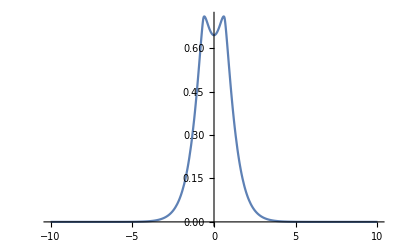
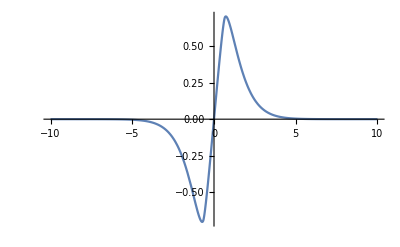
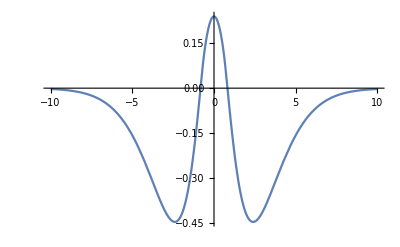
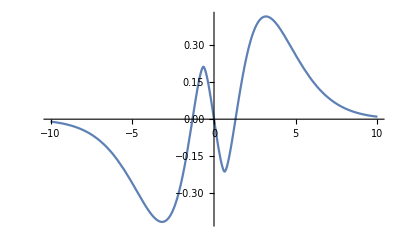

```mathematica
Table[Plot[states1to4[[i,2]][x],{x,-10,10},PlotRange->All],{i,1,4}]
```

## 2 Dimensional Hydrogen molecule ion: H_2^+

```mathematica
ℋ[ψ][{x,y},{a/2,0},{b,0},d]
```

(1/(√((-a/2+b) (-Conjugate[a]/2+Conjugate[b])))-1/(√(d^2+√((-a/2+x) (-Conjugate[a]/2+Conjugate[x])+y Conjugate[y])))-1/(√(d^2+√((-b+x) (-Conjugate[b]+Conjugate[x])+y Conjugate[y])))) ψ[{x,y}]+1/2 (-ψ^({0,2})[{x,y}]-ψ^({2,0})[{x,y}])

```mathematica
eigensystem4[ℓ_,𝓇_,ne_]:=
SortBy[
Transpose[
NDEigensystem[{ℋ[ψ][{x,y},{-𝓇/2,0},{𝓇/2,0},0.1],DirichletCondition[ψ[x,y]==0,True]},ψ,
{x,-ℓ,ℓ},{y,-ℓ,ℓ},ne,Method-> {"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}}}]],
First]
```

```mathematica
{en,wf}=eigensystem4[8.001,4,60][[1]]
```

NDEigensystem::dvlen: The function ψ[{x,y}] does not have the same number of arguments as independent variables (3).

Set::shape: Lists {en,wf} and NDEigensystem[{(1/4-1/(√Plus[«2»])-1/(√Plus[«2»])) ψ[{x,y}]+1/2 (-ψ^({«2»})[{«2»}]-ψ^({«2»})[{«2»}]),DirichletCondition[ψ[x,y]==0,True]},ψ,«3»,Method→{SpatialDiscretization→{Fin…ent,«1»}}] are not the same shape.

NDEigensystem[{(1/4-1/(√(0.01+√((-2+x) (-2+Conjugate[x])+y Conjugate[y])))-1/(√(0.01+√((2+x) (2+Conjugate[x])+y Conjugate[y])))) ψ[{x,y}]+1/2 (-ψ^({0,2})[{x,y}]-ψ^({2,0})[{x,y}]),DirichletCondition[ψ[x,y]==0,True]},ψ,{x,-8.001,8.001},{y,-8.001,8.001},60,Method→{SpatialDiscretization→{FiniteElement,{MeshOptions→{MaxCellMeasure→0.01}}}}]

Further Explorations

Name of a related topic for exploration

Name of another related topics for exploration (repeat as needed)

Authorship information

Carlos A. Arango

30/06/2017

caarango@icesi.edu.co

## On Work

WolframAlphaQueryParseResults["Polygon"]

Polygon[GeoPosition[…]]

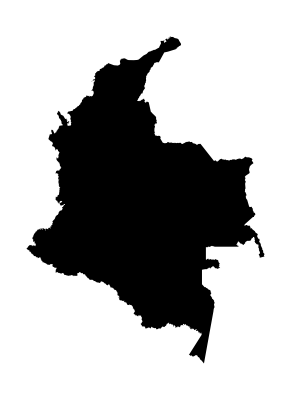

```mathematica
regcol=Graphics[Polygon[GeoPosition[…]]]
```

### Boundary conditions and integration region

Dirichlet boundary conditions exclude a region of width Δ around each H atom:

```mathematica
Subscript[ℬ, 1]={
DirichletCondition[ψ[x]==0,x≤-ℓ],
DirichletCondition[ψ[x]==0,-(𝓇+δ)/2≤x≤-(𝓇-δ)/2],
DirichletCondition[ψ[x]==0,(𝓇-δ)/2≤x≤(𝓇+δ)/2],
DirichletCondition[ψ[x]==0,x≥ℓ]
}
```

{DirichletCondition[ψ[x]==0,x≤-ℓ],DirichletCondition[ψ[x]==0,1/2 (-𝓇-δ)≤x≤1/2 (-𝓇+δ)],DirichletCondition[ψ[x]==0,(𝓇-δ)/2≤x≤(𝓇+δ)/2],DirichletCondition[ψ[x]==0,x≥ℓ]}

```mathematica
Subscript[ℬ, 2]={
DirichletCondition[ψ[x]==0,True],
DirichletCondition[ψ[x]==0,-(𝓇+δ)/2≤x≤-(𝓇-δ)/2],
DirichletCondition[ψ[x]==0,(𝓇-δ)/2≤x≤(𝓇+δ)/2]
}
```

{DirichletCondition[ψ[x]==0,True],DirichletCondition[ψ[x]==0,1/2 (-𝓇-δ)≤x≤1/2 (-𝓇+δ)],DirichletCondition[ψ[x]==0,(𝓇-δ)/2≤x≤(𝓇+δ)/2]}

Integrations region:

```mathematica
ℛ[ℓ_,𝓇_,δ_]:=Union[Interval[{-ℓ,-(𝓇+δ)/2}],Interval[{-(𝓇-δ)/2,(𝓇-δ)/2}],Interval[{(𝓇+δ)/2,ℓ}]]
```

Example:

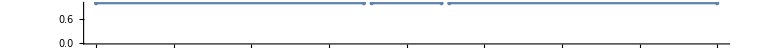

```mathematica
NumberLinePlot[ℛ[4,1,0.1]]
```